```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\THIS IS 2th line THIS ONE IS ACTUALLY JUST HD_data_wavelength_is_972.4_5_to_2 (this is in second order with 0.63 offset wavelength added after doubling the wavelength from NIST).dat

File comment header:

Spectrum #00033	11:14:35 AM 5/15/2026
Narrow scan: start 971.39nm, end 973.89nm
Monochromator settings: Grating: 1200 lines/mm; Slits: entrance 100um, exit 100um.
DAQ device: PCI-6221; ADC bits: 16; Settling time: 10ms
ADC input range: 10V max, -10V min. Sampling: 100 samples at 6.0006k/second.
Wavelength (nm)    Signal (V)

Read 115 data points.

```mathematica
?CurveFit`DataTransform
```

```mathematica
(* change the right-hand sides of the following function 
   definitions of xnew[] and ynew[] to perform the data 
   transformation you need, then evaluate this cell.      *)

xnew[ x_, y_ ] := x/2
ynew[ x_, y_ ] := y 

DataTransform[]


(* Use Undo[] if you don't like the results. *)
```

All 115 points transformed.

```mathematica
LinearDataPlot[]
```

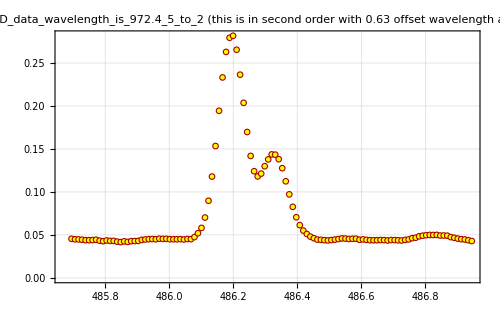

```mathematica
LinearDataPlot[]
```

```mathematica
ClearAll["Global`*"];

(* =========================*)
(*1. SET INPUT/OUTPUT FOLDER*)
(* =========================*)

inputDir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25";

outputDir=FileNameJoin[{inputDir,"PHASE1_real_wavelength_files"}];

If[DirectoryQ[outputDir],DeleteDirectory[outputDir,DeleteContents->True]];

CreateDirectory[outputDir];

subFolders={"raw_numeric_copy","real_wavelength_for_curvefit","raw_plots","real_plots"};

Scan[CreateDirectory[FileNameJoin[{outputDir,#}]]&,subFolders];

datFiles=FileNames["*.dat",inputDir];

Print["Found ",Length[datFiles]," .dat files."];


(* =========================*)
(*2. HELPER FUNCTIONS*)
(* =========================*)

importNumeric[file_]:=Module[{raw,numericRows},raw=Import[file,"Table"];
numericRows=Cases[raw,row_List/;Count[row,_?NumericQ]>=2:>Take[Cases[row,_?NumericQ],2],Infinity];
N[numericRows]];

classifyFile[file_]:=Module[{name},name=ToLowerCase[FileNameTake[file]];
Which[StringContainsQ[name,"hg"],"Hg_calibration",StringContainsQ[name,"actually just hd"],"Actual_HD_mixed_lamp",StringContainsQ[name,"hd_data"],"Hydrogen_only_control",True,"Questionable_or_excluded"]];

needsSecondOrderConversion[data_]:=Module[{center},center=Median[data[[All,1]]];
center>700];

toRealWavelength[data_]:=Module[{convertQ},convertQ=needsSecondOrderConversion[data];
If[convertQ,data/. {x_,y_}:>{x/2,y},data]];

safeString[s_]:=StringReplace[s,Except[LetterCharacter|DigitCharacter|"."|"_"|"-"]->"_"];

centerString[x_]:=StringReplace[ToString[NumberForm[N[x],{Infinity,3},NumberPoint->"."]],WhitespaceCharacter..->""];

shortBaseName[file_,index_,category_,realCenter_]:=Module[{base,center},base=StringTake[safeString[FileBaseName[file]],UpTo[55]];
center=centerString[realCenter];
IntegerString[index,10,2]<>"_"<>category<>"_"<>center<>"nm_"<>base];


(* =========================*)
(*3. PROCESS ONE FILE*)
(* =========================*)

processOneFile[file_,index_]:=Module[{raw,real,category,convertedQ,rawCenter,realCenter,base,rawOut,realOut,rawPlotOut,realPlotOut,rawPlot,realPlot,catRawDir,catRealDir,catRawPlotDir,catRealPlotDir},raw=importNumeric[file];
If[Length[raw]<5,Return[<|"index"->index,"category"->"FAILED_IMPORT","original_file"->FileNameTake[file],"n_points"->Length[raw],"raw_center_nm"->"","divided_by_2"->"","real_center_nm"->"","curvefit_ready_file"->""|>]];
category=classifyFile[file];
convertedQ=needsSecondOrderConversion[raw];
real=toRealWavelength[raw];
rawCenter=Median[raw[[All,1]]];
realCenter=Median[real[[All,1]]];
catRawDir=FileNameJoin[{outputDir,"raw_numeric_copy",category}];
catRealDir=FileNameJoin[{outputDir,"real_wavelength_for_curvefit",category}];
catRawPlotDir=FileNameJoin[{outputDir,"raw_plots",category}];
catRealPlotDir=FileNameJoin[{outputDir,"real_plots",category}];
Scan[If[!DirectoryQ[#],CreateDirectory[#]]&,{catRawDir,catRealDir,catRawPlotDir,catRealPlotDir}];
base=shortBaseName[file,index,category,realCenter];
rawOut=FileNameJoin[{catRawDir,base<>"_RAW.dat"}];
realOut=FileNameJoin[{catRealDir,base<>"_REAL_FOR_CURVEFIT.dat"}];
rawPlotOut=FileNameJoin[{catRawPlotDir,base<>"_RAW.png"}];
realPlotOut=FileNameJoin[{catRealPlotDir,base<>"_REAL.png"}];
Export[rawOut,raw,"Table"];
Export[realOut,real,"Table"];
rawPlot=ListPlot[raw,Frame->True,PlotRange->All,ImageSize->900,FrameLabel->{"Raw monochromator wavelength (nm)","Signal (V)"},PlotLabel->"RAW: "<>FileNameTake[file]];
realPlot=ListPlot[real,Frame->True,PlotRange->All,ImageSize->900,FrameLabel->{"Real wavelength after Phase 1 conversion (nm)","Signal (V)"},PlotLabel->"REAL: "<>FileNameTake[file]];
Export[rawPlotOut,rawPlot,"PNG"];
Export[realPlotOut,realPlot,"PNG"];
<|"index"->index,"category"->category,"original_file"->FileNameTake[file],"n_points"->Length[raw],"raw_center_nm"->rawCenter,"divided_by_2"->convertedQ,"real_center_nm"->realCenter,"curvefit_ready_file"->realOut|>];


(* =========================*)
(*4. RUN ON ALL FILES*)
(* =========================*)

summary=MapIndexed[processOneFile[#1,First[#2]]&,datFiles];

headers=Keys[First[summary]];
rows=Values/@summary;

Export[FileNameJoin[{outputDir,"PHASE1_summary.csv"}],Prepend[rows,headers],"CSV"];

Print["DONE."];
Print["CurveFit-ready files are saved here:"];
Print[FileNameJoin[{outputDir,"real_wavelength_for_curvefit"}]];

Dataset[summary]

SystemOpen[outputDir];
```

Found 20 .dat files.

DONE.

CurveFit-ready files are saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Actual_HD_mixed_lamp\20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.dat

Read 109 data points.

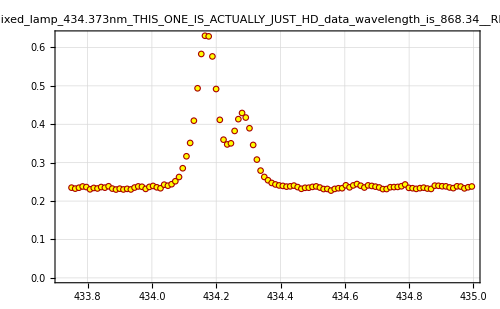

```mathematica
LinearDataPlot[]
```

```mathematica
LinearDifferencePlot[]
```

DifferencePlot::uneval: First fit the data, then plot the fit results.

$Failed

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, Nonstandard -> True, DataFunction -> FreqResp]]
]
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Actual_HD_mixed_lamp\20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.dat

Read 109 data points.

```mathematica
LinearDataPlot[]
```

-Graphics-

```mathematica
Export["C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files\\real_wavelength_for_curvefit\\Actual_HD_mixed_lamp\\20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.pdf",%44,"PDF"]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Actual_HD_mixed_lamp\20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.pdf

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Actual_HD_mixed_lamp\20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.dat

Read 109 data points.

```mathematica
LinearDataPlot[]
```

-Graphics-

```mathematica
ClearAll["Global`*"];

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

dataRoot=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit"}];

pdfRoot=FileNameJoin[{phase1Dir,"PDF_plots_for_report"}];

If[!DirectoryQ[pdfRoot],CreateDirectory[pdfRoot]];

files=FileNames["*_REAL_FOR_CURVEFIT.dat",dataRoot,Infinity];

Print["Found ",Length[files]," converted data files."];

makePDF[file_]:=Module[{data,category,outDir,outFile,plot},data=Import[file,"Table"];
data=Cases[data,{x_?NumericQ,y_?NumericQ,___}:>{x,y},Infinity];
category=FileNameSplit[DirectoryName[file]][[-1]];
outDir=FileNameJoin[{pdfRoot,category}];
If[!DirectoryQ[outDir],CreateDirectory[outDir]];
outFile=FileNameJoin[{outDir,FileBaseName[file]<>".pdf"}];
plot=ListPlot[data,Frame->True,PlotRange->All,ImageSize->900,FrameLabel->{"Real wavelength (nm)","Signal (V)"},PlotLabel->FileBaseName[file]];
Export[outFile,plot,"PDF"];
outFile];

exportedPDFs=makePDF/@files;

Print["DONE. PDFs saved here:"];
Print[pdfRoot];

SystemOpen[pdfRoot];
```

Found 20 converted data files.

DONE. PDFs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PDF_plots_for_report

```mathematica
ClearAll["Global`*"];

curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";

SetDirectory[curveFitDir];

Print["Loading CurveFit package..."];
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

Print["---- Lines in Palette.m mentioning Linear Plot ----"];
Print/@FindList[FileNameJoin[{curveFitDir,"Palette.m"}],"Linear Plot",20];

Print["---- Lines in Plots.m mentioning Linear ----"];
Print/@FindList[FileNameJoin[{curveFitDir,"Plots.m"}],"Linear",30];

Print["---- Possible plotting function names ----"];
Names["Global`*Plot*"]//Sort//Column

Print["---- Possible data function names ----"];
Names["Global`*Data*"]//Sort//Column
```

Loading CurveFit package...

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

---- Lines in Palette.m mentioning Linear Plot ----

"Linear Plot"            :> eval["LinearDataPlot[]"],

---- Lines in Plots.m mentioning Linear ----

"\!\(\*StyleBox[\"LinearDataPlot\",\nFontFamily->\"Courier\"]\)"<>

"\!\(\*StyleBox[\"LinearDataPlot\",\nFontFamily->\"Courier\"]\) "<>

"\!\(\*StyleBox[\"LinearDataPlot\",\nFontFamily->\"Courier\"]\)"<>

"\!\(\*StyleBox[\"LinearDataPlot\",\nFontFamily->\"Courier\"]\) "<>

"\!\(\*StyleBox[\"LinearDataPlot\",\nFontFamily->\"Courier\"]\) "<>

"\!\(\*StyleBox[\"LinearDataPlot[Tips -> All]\",\nFontFamily->\"Courier\"]\) "<>

"\!\(\*StyleBox[\"LinearDataPlot\",\nFontFamily->\"Courier\"]\), "<>

LinearDataPlot::usage =

"\!\(\*StyleBox[\"LinearDataPlot\",\nFontFamily->\"Courier\"]\)"<>

"\!\(\*StyleBox[\"LinearDataPlot\",\nFontFamily->\"Courier\"]\)"<>

"\!\(\*StyleBox[\"LinearDataPlot\",\nFontFamily->\"Courier\"]\)"<>

"Tips, DataSizeThreshold, BackupData, LinearDifferencePlot";

LogLinearDataPlot::usage =

"\!\(\*StyleBox[\"LogLinearDataPlot\",\nFontFamily->\"Courier\"]\)"<>

"\!\(\*StyleBox[\"LogLinearDataPlot\",\nFontFamily->\"Courier\"]\)"<>

"\!\(\*StyleBox[\"LogLinearDataPlot\",\nFontFamily->\"Courier\"]\)"<>

"Tips, DataSizeThreshold, BackupData, LogLinearDifferencePlot";

"generated by LinearDifferencePlot, etc.";

"generated by LinearDifferencePlot, etc.";

LinearDifferencePlot::usage =

"LinearDifferencePlot[ ] "<>

LogLinearDifferencePlot::usage =

"LogLinearDifferencePlot[ ] "<>

Plot, LogPlot, LogLinearPlot, LogLogPlot, ParametricPlot

ListPlot, ListLogPlot, ListLogLinearPlot, ListLogLogPlot

LinearDataPlot, LogDataPlot, LogLinearDataPlot, LogLogDataPlot, ScatterDataPlot,

LinearDifferencePlot, LogDifferencePlot, LogLinearDifferencePlot, LogLogDifferencePlot,

LinearDataPlot[ opts:OptionsPattern[] ] := DataPlot[ListPlot, opts]

LinearDataPlot[d:PlotDataFormat[], opts:OptionsPattern[]] := DataPlot[ListPlot, d, opts]

LogLinearDataPlot[ opts:OptionsPattern[] ] := DataPlot[ListLogLinearPlot, opts]

---- Possible plotting function names ----

catRawPlotDir
catRawPlotDir$
catRealPlotDir
catRealPlotDir$
rawPlot
rawPlotOut
rawPlotOut$
rawPlot$
realPlot
realPlotOut
realPlotOut$
realPlot$

---- Possible data function names ----

```mathematica
ClearAll["Global`*"];

curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

file="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files\\real_wavelength_for_curvefit\\Actual_HD_mixed_lamp\\PUT_ONE_FILE_NAME_HERE.dat";

data=Import[file,"Table"];
data=Cases[data,{x_?NumericQ,y_?NumericQ,___}:>{x,y},Infinity];

(*CurveFit usually uses these global arrays*)
xx=data[[All,1]];
yy=data[[All,2]];

(*fake zero errors,just so CurveFit has something if it expects them*)
sx=ConstantArray[0,Length[xx]];
sy=ConstantArray[0,Length[yy]];

LinearDataPlot[]
```

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Import::nffil: File C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Actual_HD_mixed_lamp\PUT_ONE_FILE_NAME_HERE.dat not found during Import.

CheckLength::empty: The data set is empty. Load data and try again.

$Failed

```mathematica
ClearAll["Global`*"];

curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

actualHDDir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files\\real_wavelength_for_curvefit\\Actual_HD_mixed_lamp";

files=FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir];

Print["Found files:"];
Column[FileNameTake/@files]

file=First[files];

Print["Using file:"];
Print[file];

data=Import[file,"Table"];
data=Cases[data,{x_?NumericQ,y_?NumericQ,___}:>{x,y},Infinity];

Print["Number of points = ",Length[data]];
Print["x range = ",MinMax[data[[All,1]]]];
Print["y range = ",MinMax[data[[All,2]]]];

xx=data[[All,1]];
yy=data[[All,2]];
sx=ConstantArray[0,Length[xx]];
sy=ConstantArray[0,Length[yy]];

LinearDataPlot[]
```

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Found files:

01_Actual_HD_mixed_lamp_388.945nm_100_slit_width_THIS_IS_6th_line_THIS_ONE_IS_ACTUALLY_JU_REAL_FOR_CURVEFIT.dat
02_Actual_HD_mixed_lamp_410.500nm_100_sliut_width_and_4th_line_THIS_ONE_IS_ACTUALLY_JUST__REAL_FOR_CURVEFIT.dat
16_Actual_HD_mixed_lamp_656.495nm_THIS_IS_1th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat
17_Actual_HD_mixed_lamp_486.320nm_THIS_IS_2th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat
18_Actual_HD_mixed_lamp_388.945nm_THIS_IS_6th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat
19_Actual_HD_mixed_lamp_397.413nm_THIS_ONE_IS_ACTUALLY_JUST_HD_5th_layer_100_nm_width_of__REAL_FOR_CURVEFIT.dat
20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.dat

Using file:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Actual_HD_mixed_lamp\01_Actual_HD_mixed_lamp_388.945nm_100_slit_width_THIS_IS_6th_line_THIS_ONE_IS_ACTUALLY_JU_REAL_FOR_CURVEFIT.dat

Number of points = 105

x range = {388.32,389.57}

y range = {0.051641,4.62711}

CheckLength::unequal: It must be: n = Length[xx] = Length[yy] = Length[sy] = Length[sx]

$Failed

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

n = 105

Lengths = {105,105,105,105}

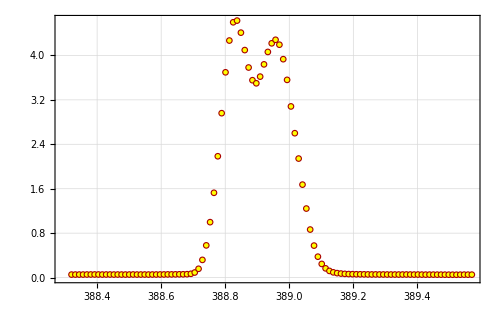

```mathematica
ClearAll["Global`*"];

curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

actualHDDir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files\\real_wavelength_for_curvefit\\Actual_HD_mixed_lamp";

files=FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir];

file=First[files];

data=Import[file,"Table"];
data=Cases[data,{x_?NumericQ,y_?NumericQ,___}:>{x,y},Infinity];

n=Length[data];

xx=data[[All,1]];
yy=data[[All,2]];
sx=ConstantArray[0.,n];
sy=ConstantArray[0.,n];

Print["n = ",n];
Print["Lengths = ",Length/@{xx,yy,sx,sy}];

LinearDataPlot[]
```

```mathematica
ClearAll["Global`*"];

(*Load CurveFit package*)
curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

(*Folder containing converted real-wavelength files*)
phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

dataRoot=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit"}];

(*Output folder for PDFs*)
pdfRoot=FileNameJoin[{phase1Dir,"CurveFit_default_linear_plot_PDFs"}];

If[DirectoryQ[pdfRoot],DeleteDirectory[pdfRoot,DeleteContents->True]];

CreateDirectory[pdfRoot];

files=FileNames["*_REAL_FOR_CURVEFIT.dat",dataRoot,Infinity];

Print["Found ",Length[files]," converted data files."];

makeCurveFitPDF[file_]:=Module[{data,category,outDir,outFile,plot},data=Import[file,"Table"];
data=Cases[data,{x_?NumericQ,y_?NumericQ,___}:>{x,y},Infinity];
If[Length[data]<3,Print["Skipping bad file: ",FileNameTake[file]];
Return[$Failed];];
(*CurveFit global variables*)n=Length[data];
xx=data[[All,1]];
yy=data[[All,2]];
sx=ConstantArray[0.,n];
sy=ConstantArray[0.,n];
category=FileNameSplit[DirectoryName[file]][[-1]];
outDir=FileNameJoin[{pdfRoot,category}];
If[!DirectoryQ[outDir],CreateDirectory[outDir]];
plot=Quiet[LinearDataPlot[],{SetOptions::optnf}];
outFile=FileNameJoin[{outDir,FileBaseName[file]<>".pdf"}];
Export[outFile,plot,"PDF"];
Print["Saved: ",outFile];
outFile];

exported=DeleteCases[makeCurveFitPDF/@files,$Failed];

Print["DONE. Exported ",Length[exported]," PDFs."];
Print["Saved here:"];
Print[pdfRoot];

SystemOpen[pdfRoot];
```

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Found 20 converted data files.

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Actual_HD_mixed_lamp\01_Actual_HD_mixed_lamp_388.945nm_100_slit_width_THIS_IS_6th_line_THIS_ONE_IS_ACTUALLY_JU_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Actual_HD_mixed_lamp\02_Actual_HD_mixed_lamp_410.500nm_100_sliut_width_and_4th_line_THIS_ONE_IS_ACTUALLY_JUST__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Actual_HD_mixed_lamp\16_Actual_HD_mixed_lamp_656.495nm_THIS_IS_1th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Actual_HD_mixed_lamp\17_Actual_HD_mixed_lamp_486.320nm_THIS_IS_2th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Actual_HD_mixed_lamp\18_Actual_HD_mixed_lamp_388.945nm_THIS_IS_6th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Actual_HD_mixed_lamp\19_Actual_HD_mixed_lamp_397.413nm_THIS_ONE_IS_ACTUALLY_JUST_HD_5th_layer_100_nm_width_of__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Actual_HD_mixed_lamp\20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hg_calibration\03_Hg_calibration_365.365nm_365.12_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hg_calibration\04_Hg_calibration_365.835nm_365.588_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hg_calibration\05_Hg_calibration_405.020nm_404.770_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hg_calibration\06_Hg_calibration_546.475nm_546.226_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hg_calibration\07_Hg_calibration_546.250nm_562hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hg_calibration\15_Hg_calibration_546.250nm_same_data_as_562hg_2nm_scan_but_slit_width_is_20_nm_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hydrogen_only_control\08_Hydrogen_only_control_656.695nm_HD_data_wavelength_is_1313.15_3_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hydrogen_only_control\09_Hydrogen_only_control_656.525nm_HD_data_wavelength_is_656.279_3_to_2_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hydrogen_only_control\10_Hydrogen_only_control_389.035nm_HD_data_wavelength_is_777.637_7_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hydrogen_only_control\11_Hydrogen_only_control_397.765nm_HD_data_wavelength_is_794.566_6_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hydrogen_only_control\12_Hydrogen_only_control_410.470nm_HD_data_wavelength_is_820.752_5_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hydrogen_only_control\13_Hydrogen_only_control_434.608nm_HD_data_wavelength_is_868.34_5_to_2__this_is_in_second__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs\Hydrogen_only_control\14_Hydrogen_only_control_486.418nm_HD_data_wavelength_is_972.59_4_to_2__this_is_in_second__REAL_FOR_CURVEFIT.pdf

DONE. Exported 20 PDFs.

Saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_default_linear_plot_PDFs

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\Stacked_overview_plots\01_Hg_calibration_stacked.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\Stacked_overview_plots\02_Hydrogen_only_control_stacked.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\Stacked_overview_plots\03_Actual_HD_mixed_lamp_stacked.pdf

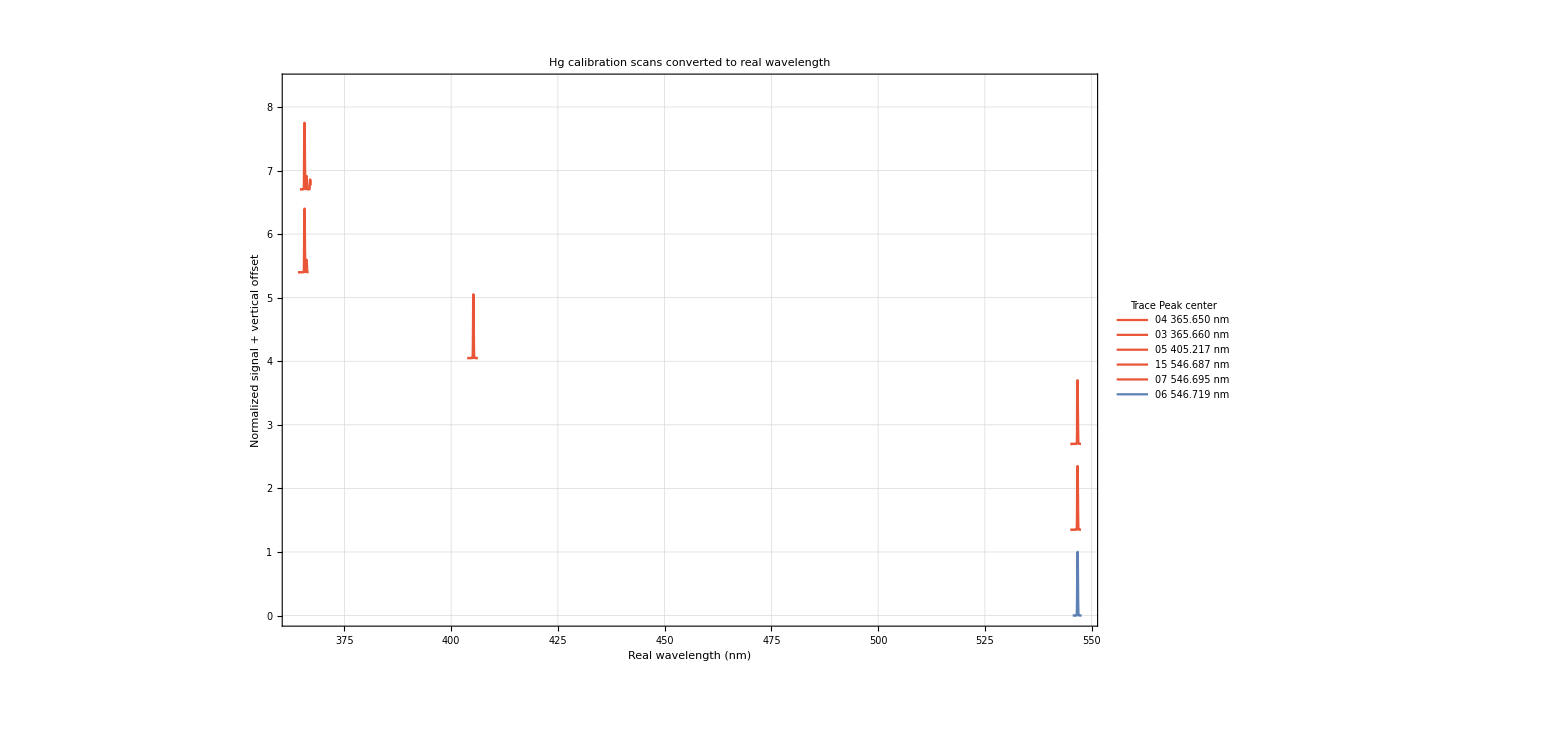
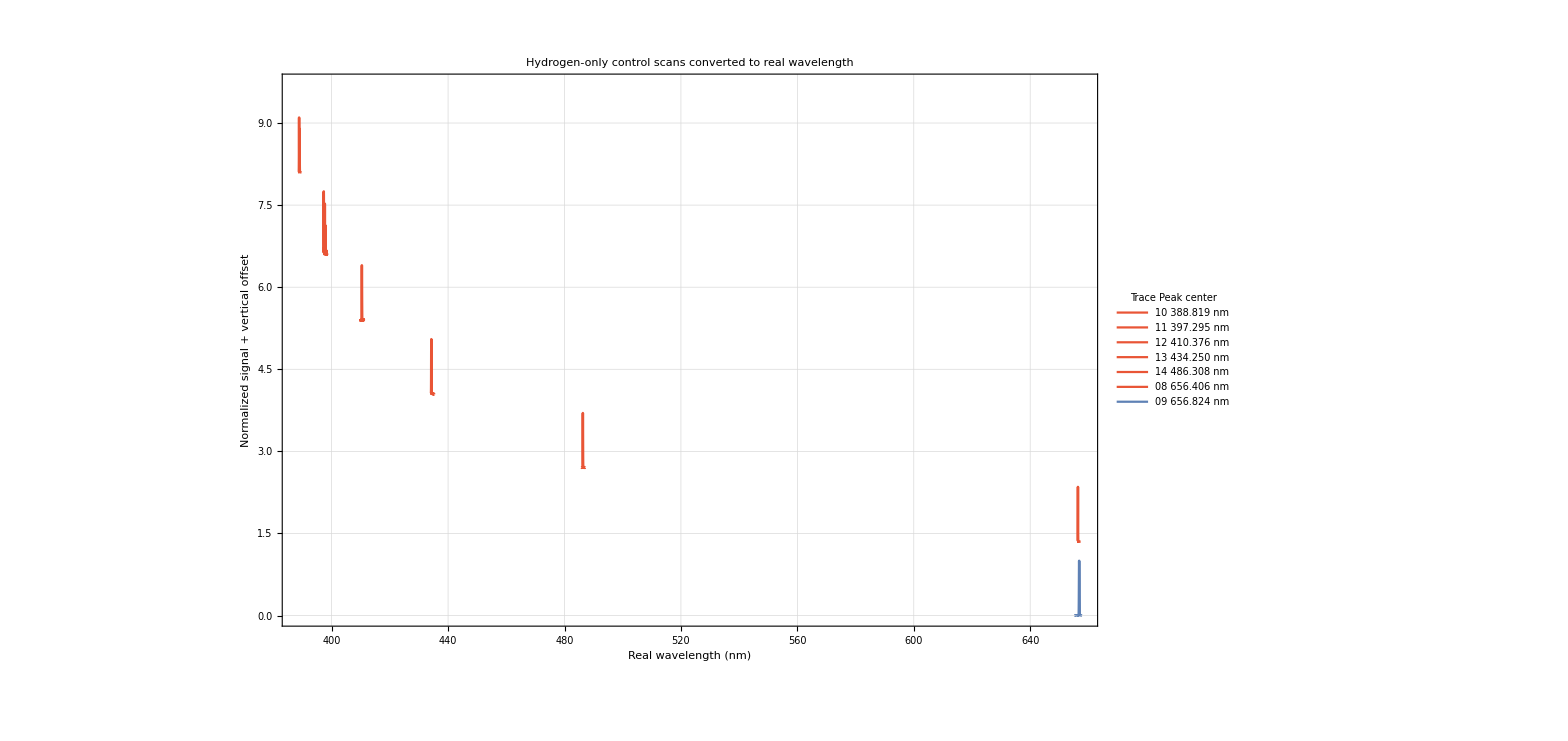
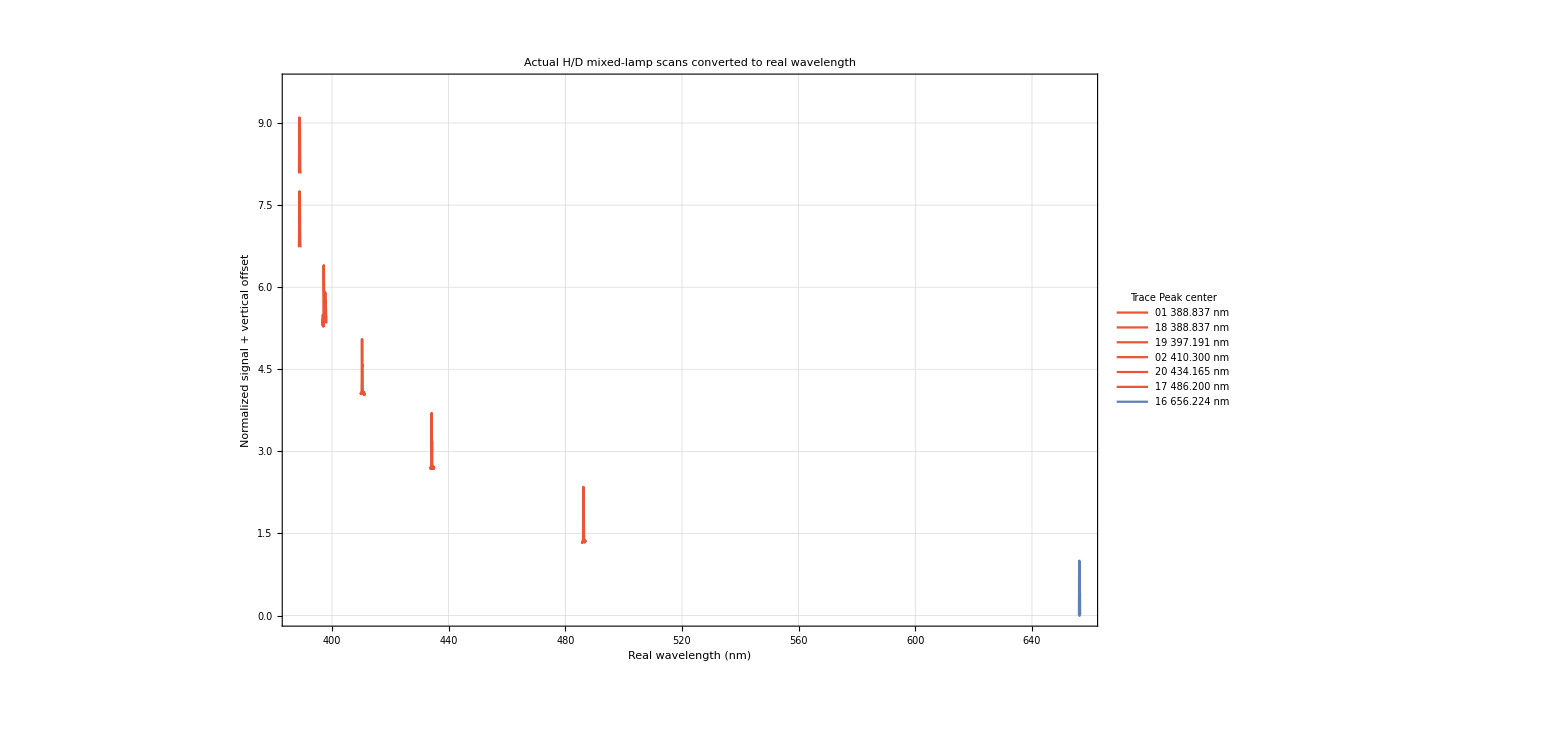

```mathematica
ClearAll["Global`*"];

(* =========================================*)
(*1. FOLDERS*)
(* =========================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

dataRoot=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit"}];

stackRoot=FileNameJoin[{phase1Dir,"Stacked_overview_plots"}];

If[DirectoryQ[stackRoot],DeleteDirectory[stackRoot,DeleteContents->True]];
CreateDirectory[stackRoot];

(* =========================================*)
(*2. HELPERS*)
(* =========================================*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
d=Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity];
SortBy[d,First]];

baselineSubtractNormalize[data_]:=Module[{x,y,nEdge,base,y0,amp},{x,y}=Transpose[data];
nEdge=Max[3,Min[10,Floor[Length[data]/8]]];
base=Mean@Join[Take[y,nEdge],Take[y,-nEdge]];
y0=y-base;
amp=Max[y0];
If[amp<=0,amp=1.0];
Transpose[{x,y0/amp}]];

peakCenter[data_]:=Module[{i},i=Ordering[data[[All,2]],-1][[1]];
data[[i,1]]];

shortLabel[file_,center_]:=Module[{idx},idx=First@StringSplit[FileBaseName[file],"_"];
idx<>"   "<>ToString[NumberForm[center,{Infinity,3}]]<>" nm"];

makeStackedPlot[category_String,mainTitle_String,outStem_String,spacing_:1.35]:=Module[{folder,files,rawData,procData,centers,order,labels,offsets,shifted,colors,xMin,xMax,yMax,legend,plot,outPDF,outPNG},folder=FileNameJoin[{dataRoot,category}];
files=FileNames["*_REAL_FOR_CURVEFIT.dat",folder];
If[Length[files]==0,Print["No files found in: ",folder];
Return[$Failed];];
rawData=importNumeric/@files;
procData=baselineSubtractNormalize/@rawData;
centers=peakCenter/@procData;
order=Ordering[centers];
files=files[[order]];
rawData=rawData[[order]];
procData=procData[[order]];
centers=centers[[order]];
labels=MapThread[shortLabel,{files,centers}];
offsets=Reverse[Range[0,spacing (Length[procData]-1),spacing]];
shifted=MapThread[(#1/. {x_,y_}:>{x,y+#2})&,{procData,offsets}];
colors=ColorData[97]/@Rescale[Range[Length[shifted]]];
xMin=Min[Flatten[shifted[[All,All,1]]]];
xMax=Max[Flatten[shifted[[All,All,1]]]];
yMax=Max[Flatten[shifted[[All,All,2]]]]+0.6;
legend=LineLegend[colors,labels,LegendLabel->Style["Trace   Peak center",11,Bold],LabelStyle->Directive[11],LegendFunction->"Frame"];
plot=ListLinePlot[shifted,Frame->True,Axes->False,PlotRange->{{xMin,xMax},{0,yMax}},PlotStyle->(Directive[#,AbsoluteThickness[1.8]]&/@colors),GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.83]],Background->White,ImageSize->1200,FrameStyle->Directive[Black,AbsoluteThickness[1]],LabelStyle->Directive[Black,12],FrameLabel->{Style["Real wavelength (nm)",Italic,13],Style["Normalized signal + vertical offset",Italic,13]},PlotLabel->Style[mainTitle,15,Bold],PlotLegends->Placed[legend,Right],ImagePadding->{{70,250},{60,30}}];
outPDF=FileNameJoin[{stackRoot,outStem<>".pdf"}];
outPNG=FileNameJoin[{stackRoot,outStem<>".png"}];
Export[outPDF,plot,"PDF"];
Export[outPNG,plot,"PNG"];
Print["Saved: ",outPDF];
plot];

(* =========================================*)
(*3. MAKE THE THREE STACKED PLOTS*)
(* =========================================*)

hgPlot=makeStackedPlot["Hg_calibration","Hg calibration scans converted to real wavelength","01_Hg_calibration_stacked"];

hOnlyPlot=makeStackedPlot["Hydrogen_only_control","Hydrogen-only control scans converted to real wavelength","02_Hydrogen_only_control_stacked"];

hdPlot=makeStackedPlot["Actual_HD_mixed_lamp","Actual H/D mixed-lamp scans converted to real wavelength","03_Actual_HD_mixed_lamp_stacked"];

(* =========================================*)
(*4. SHOW THEM IN THE NOTEBOOK*)
(* =========================================*)

Column[{hgPlot,hOnlyPlot,hdPlot},Spacings->2]

SystemOpen[stackRoot];
```

```mathematica
ClearAll["Global`*"];

(*Load CurveFit package*)
curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

(*Folder containing converted real-wavelength files*)
phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

dataRoot=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit"}];

(*Output folder*)
pdfRoot=FileNameJoin[{phase1Dir,"CurveFit_titled_linear_plot_PDFs"}];

If[DirectoryQ[pdfRoot],DeleteDirectory[pdfRoot,DeleteContents->True]];

CreateDirectory[pdfRoot];

files=FileNames["*_REAL_FOR_CURVEFIT.dat",dataRoot,Infinity];

Print["Found ",Length[files]," converted data files."];

makeTitledCurveFitPDF[file_]:=Module[{data,category,outDir,outFile,baseTitle,plot,titledPlot},data=Import[file,"Table"];
data=Cases[data,{x_?NumericQ,y_?NumericQ,___}:>{x,y},Infinity];
If[Length[data]<3,Print["Skipping bad file: ",FileNameTake[file]];
Return[$Failed];];
(*CurveFit globals*)n=Length[data];
xx=data[[All,1]];
yy=data[[All,2]];
sx=ConstantArray[0.,n];
sy=ConstantArray[0.,n];
category=FileNameSplit[DirectoryName[file]][[-1]];
outDir=FileNameJoin[{pdfRoot,category}];
If[!DirectoryQ[outDir],CreateDirectory[outDir]];
baseTitle=FileBaseName[file];
plot=Quiet[LinearDataPlot[],{SetOptions::optnf}];
titledPlot=Labeled[plot,Style[baseTitle,12,Italic,Black,FontFamily->"Times"],Top];
outFile=FileNameJoin[{outDir,baseTitle<>".pdf"}];
Export[outFile,titledPlot,"PDF"];
Print["Saved: ",outFile];
outFile];

exported=DeleteCases[makeTitledCurveFitPDF/@files,$Failed];

Print["DONE. Exported ",Length[exported]," titled PDFs."];
Print["Saved here:"];
Print[pdfRoot];

SystemOpen[pdfRoot];
```

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Found 20 converted data files.

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Actual_HD_mixed_lamp\01_Actual_HD_mixed_lamp_388.945nm_100_slit_width_THIS_IS_6th_line_THIS_ONE_IS_ACTUALLY_JU_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Actual_HD_mixed_lamp\02_Actual_HD_mixed_lamp_410.500nm_100_sliut_width_and_4th_line_THIS_ONE_IS_ACTUALLY_JUST__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Actual_HD_mixed_lamp\16_Actual_HD_mixed_lamp_656.495nm_THIS_IS_1th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Actual_HD_mixed_lamp\17_Actual_HD_mixed_lamp_486.320nm_THIS_IS_2th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Actual_HD_mixed_lamp\18_Actual_HD_mixed_lamp_388.945nm_THIS_IS_6th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Actual_HD_mixed_lamp\19_Actual_HD_mixed_lamp_397.413nm_THIS_ONE_IS_ACTUALLY_JUST_HD_5th_layer_100_nm_width_of__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Actual_HD_mixed_lamp\20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hg_calibration\03_Hg_calibration_365.365nm_365.12_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hg_calibration\04_Hg_calibration_365.835nm_365.588_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hg_calibration\05_Hg_calibration_405.020nm_404.770_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hg_calibration\06_Hg_calibration_546.475nm_546.226_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hg_calibration\07_Hg_calibration_546.250nm_562hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hg_calibration\15_Hg_calibration_546.250nm_same_data_as_562hg_2nm_scan_but_slit_width_is_20_nm_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hydrogen_only_control\08_Hydrogen_only_control_656.695nm_HD_data_wavelength_is_1313.15_3_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hydrogen_only_control\09_Hydrogen_only_control_656.525nm_HD_data_wavelength_is_656.279_3_to_2_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hydrogen_only_control\10_Hydrogen_only_control_389.035nm_HD_data_wavelength_is_777.637_7_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hydrogen_only_control\11_Hydrogen_only_control_397.765nm_HD_data_wavelength_is_794.566_6_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hydrogen_only_control\12_Hydrogen_only_control_410.470nm_HD_data_wavelength_is_820.752_5_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hydrogen_only_control\13_Hydrogen_only_control_434.608nm_HD_data_wavelength_is_868.34_5_to_2__this_is_in_second__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs\Hydrogen_only_control\14_Hydrogen_only_control_486.418nm_HD_data_wavelength_is_972.59_4_to_2__this_is_in_second__REAL_FOR_CURVEFIT.pdf

DONE. Exported 20 titled PDFs.

Saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_titled_linear_plot_PDFs

```mathematica
ClearAll["Global`*"];

(*Load CurveFit*)
curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

(*Existing folders*)
phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

realRoot=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit"}];
rawRoot=FileNameJoin[{phase1Dir,"raw_numeric_copy"}];

(*New output folder:this does NOT touch your existing data/plots*)
outRoot=FileNameJoin[{phase1Dir,"CurveFit_before_after_PDFs"}];
If[!DirectoryQ[outRoot],CreateDirectory[outRoot]];

(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

balmerRefs={{"Hα",656.28},{"Hβ",486.13},{"Hγ",434.05},{"Hδ",410.17},{"Hϵ",397.01},{"Hζ",388.91}};

closestBalmer[w_]:=Module[{c},c=First@SortBy[balmerRefs,Abs[#[[2]]-w]&];
If[Abs[c[[2]]-w]<=3,c[[1]],None]];

nmString[x_]:=ToString@NumberForm[N[x],{6,3},NumberPadding->{"","0"}];

cleanTitle[category_,realCenter_]:=Module[{b},b=closestBalmer[realCenter];
Switch[category,"Hg_calibration","Hg calibration scan: "<>ToString@NumberForm[realCenter,{5,1}]<>" nm region","Hydrogen_only_control","Hydrogen-only control: "<>If[b=!=None,b<>" region (~"<>nmString[realCenter]<>" nm)","~"<>nmString[realCenter]<>" nm region"],"Actual_HD_mixed_lamp","Hydrogen-deuterium mixed lamp: "<>If[b=!=None,b<>" region (~"<>nmString[realCenter]<>" nm)","~"<>nmString[realCenter]<>" nm region"],_,category<>": ~"<>nmString[realCenter]<>" nm region"]];

curveFitGraphic[data_,panelTitle_]:=Module[{g},n=Length[data];
xx=data[[All,1]];
yy=data[[All,2]];
sx=ConstantArray[0.,n];
sy=ConstantArray[0.,n];
g=Quiet[LinearDataPlot[],{SetOptions::optnf}];
Show[g,PlotLabel->Style[panelTitle,12,Italic,Black,FontFamily->"Times"],ImageSize->800]];

pairedFigure[rawData_,realData_,mainTitle_]:=Module[{topPlot,bottomPlot,note},topPlot=curveFitGraphic[rawData,"Before conversion: instrument wavelength (2nd order)"];
bottomPlot=curveFitGraphic[realData,"After conversion: real wavelength = instrument wavelength / 2"];
note=Style["Top panel: before conversion (instrument wavelength, 2nd order).   Bottom panel: after conversion (real wavelength = instrument wavelength / 2).",10,Black,FontFamily->"Times"];
Labeled[Labeled[GraphicsColumn[{topPlot,bottomPlot},Spacings->0.45],Style[mainTitle,13,Black,FontFamily->"Times"],Top],note,Bottom]];

makePairedPDF[realFile_]:=Module[{category,realData,realCenter,rawFileBase,rawFile,rawData,title,outDir,outFile,fig},category=FileNameSplit[DirectoryName[realFile]][[-1]];
realData=importNumeric[realFile];
If[Length[realData]<3,Print["Skipping bad real file: ",FileNameTake[realFile]];
Return[$Failed];];
realCenter=Median[realData[[All,1]]];
rawFileBase=StringReplace[FileBaseName[realFile],"_REAL_FOR_CURVEFIT"->"_RAW"]<>".dat";
rawFile=FileNameJoin[{rawRoot,category,rawFileBase}];
If[!FileExistsQ[rawFile],Print["Missing raw file for: ",FileNameTake[realFile]];
Return[$Failed];];
rawData=importNumeric[rawFile];
If[Length[rawData]<3,Print["Skipping bad raw file: ",FileNameTake[rawFile]];
Return[$Failed];];
title=cleanTitle[category,realCenter];
fig=pairedFigure[rawData,realData,title];
outDir=FileNameJoin[{outRoot,category}];
If[!DirectoryQ[outDir],CreateDirectory[outDir]];
outFile=FileNameJoin[{outDir,FileBaseName[realFile]<>".pdf"}];
Export[outFile,fig,"PDF"];
Print["Saved: ",outFile];
outFile];

(*----------run on all converted files----------*)

files=FileNames["*_REAL_FOR_CURVEFIT.dat",realRoot,Infinity];

Print["Found ",Length[files]," converted files."];

exported=DeleteCases[makePairedPDF/@files,$Failed];

Print["DONE. Exported ",Length[exported]," paired before/after PDFs."];
Print["Saved here: ",outRoot];

SystemOpen[outRoot];
```

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Found 20 converted files.

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Actual_HD_mixed_lamp\01_Actual_HD_mixed_lamp_388.945nm_100_slit_width_THIS_IS_6th_line_THIS_ONE_IS_ACTUALLY_JU_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Actual_HD_mixed_lamp\02_Actual_HD_mixed_lamp_410.500nm_100_sliut_width_and_4th_line_THIS_ONE_IS_ACTUALLY_JUST__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Actual_HD_mixed_lamp\16_Actual_HD_mixed_lamp_656.495nm_THIS_IS_1th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Actual_HD_mixed_lamp\17_Actual_HD_mixed_lamp_486.320nm_THIS_IS_2th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Actual_HD_mixed_lamp\18_Actual_HD_mixed_lamp_388.945nm_THIS_IS_6th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Actual_HD_mixed_lamp\19_Actual_HD_mixed_lamp_397.413nm_THIS_ONE_IS_ACTUALLY_JUST_HD_5th_layer_100_nm_width_of__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Actual_HD_mixed_lamp\20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hg_calibration\03_Hg_calibration_365.365nm_365.12_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hg_calibration\04_Hg_calibration_365.835nm_365.588_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hg_calibration\05_Hg_calibration_405.020nm_404.770_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hg_calibration\06_Hg_calibration_546.475nm_546.226_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hg_calibration\07_Hg_calibration_546.250nm_562hg_2nm_scan_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hg_calibration\15_Hg_calibration_546.250nm_same_data_as_562hg_2nm_scan_but_slit_width_is_20_nm_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hydrogen_only_control\08_Hydrogen_only_control_656.695nm_HD_data_wavelength_is_1313.15_3_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hydrogen_only_control\09_Hydrogen_only_control_656.525nm_HD_data_wavelength_is_656.279_3_to_2_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hydrogen_only_control\10_Hydrogen_only_control_389.035nm_HD_data_wavelength_is_777.637_7_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hydrogen_only_control\11_Hydrogen_only_control_397.765nm_HD_data_wavelength_is_794.566_6_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hydrogen_only_control\12_Hydrogen_only_control_410.470nm_HD_data_wavelength_is_820.752_5_to_2__this_is_in_second_REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hydrogen_only_control\13_Hydrogen_only_control_434.608nm_HD_data_wavelength_is_868.34_5_to_2__this_is_in_second__REAL_FOR_CURVEFIT.pdf

Saved: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs\Hydrogen_only_control\14_Hydrogen_only_control_486.418nm_HD_data_wavelength_is_972.59_4_to_2__this_is_in_second__REAL_FOR_CURVEFIT.pdf

DONE. Exported 20 paired before/after PDFs.

Saved here: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\CurveFit_before_after_PDFs

```mathematica
ClearAll["Global`*"];

(* ===============================*)
(*CURVEFIT PACKAGE INSPECTION*)
(* ===============================*)

pkgRoot="C:\\Users\\ansht\\Desktop\\package\\CurveFit";

timeStamp=DateString[{"Year","Month","Day","_","Hour","Minute","Second"}];

outRoot=FileNameJoin[{pkgRoot,"INSPECTION_"<>timeStamp}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

Print["Inspection output folder:"];
Print[outRoot];

mFiles=Sort@FileNames["*.m",pkgRoot,Infinity];

Print["Found .m files:"];
Column[FileNameDrop[#,FileNameDepth[pkgRoot]]&/@mFiles]


(* ===============================*)
(*BASIC FILE CATALOG*)
(* ===============================*)

readText[file_]:=Import[file,"Text"];

readLines[file_]:=StringSplit[readText[file],{"\r\n","\n","\r"}];

fileCatalog=Table[Module[{txt=readText[f],lines},lines=readLines[f];
{FileNameDrop[f,FileNameDepth[pkgRoot]],FileByteCount[f],Length[lines],StringCount[txt,"\n"]}],{f,mFiles}];

Export[FileNameJoin[{outRoot,"01_file_catalog.csv"}],Prepend[fileCatalog,{"relative_file","bytes","line_count","newline_count"}],"CSV"];


(* ===============================*)
(*SEARCH SOURCE FOR IMPORTANT TERMS*)
(* ===============================*)

terms={"Gaussian","Gauss","Lorentz","Polynomial","Fit","User-defined","UserDefined","Nonlinear","LinearModelFit","FindFit","FitResults","Parameter","ParameterTable","ParameterErrors","Covariance","Correlation","Residual","Difference","Chi","StandardDeviation","LinearDataPlot","DataPlot","LinearDifferencePlot","DataTransform","Analyze Y data","assign","sigma","sx","sy","xx","yy","n="};

sourceHits=Flatten[Table[Module[{lines=readLines[f],rel},rel=FileNameDrop[f,FileNameDepth[pkgRoot]];
Flatten[Table[If[StringContainsQ[lines[[i]],term,IgnoreCase->True],{{rel,i,term,StringTrim[lines[[i]]]}},{}],{i,Length[lines]},{term,terms}],1]],{f,mFiles}],1];

Export[FileNameJoin[{outRoot,"02_source_term_hits.csv"}],Prepend[sourceHits,{"relative_file","line_number","matched_term","line_text"}],"CSV"];

Print["Term hits exported: ",Length[sourceHits]];


(* ===============================*)
(*FIND POSSIBLE FUNCTION DEFINITIONS*)
(* ===============================*)

definitionRegex=RegularExpression["^\\s*([A-Za-z\\$][A-Za-z0-9\\$]*)\\s*(\\[|::usage|:=|=)"];

definitionHits=Flatten[Table[Module[{lines=readLines[f],rel},rel=FileNameDrop[f,FileNameDepth[pkgRoot]];
Flatten[Table[With[{m=StringCases[lines[[i]],definitionRegex->"$1"]},If[Length[m]>0,{{rel,i,First[m],StringTrim[lines[[i]]]}},{}]],{i,Length[lines]}],1]],{f,mFiles}],1];

definitionHits=DeleteDuplicates[definitionHits];

Export[FileNameJoin[{outRoot,"03_possible_function_definitions.csv"}],Prepend[definitionHits,{"relative_file","line_number","symbol","line_text"}],"CSV"];

Print["Possible definitions exported: ",Length[definitionHits]];


(* ===============================*)
(*LOAD CURVEFIT AND INSPECT SYMBOLS*)
(* ===============================*)

SetDirectory[pkgRoot];

Print["Loading CurveFit.m..."];
Quiet[Get[FileNameJoin[{pkgRoot,"CurveFit.m"}]],{SetOptions::optnf}];

loadedSymbols=Sort@Names["Global`*"];

Print["Loaded Global symbols: ",Length[loadedSymbols]];

keywords={"fit","gauss","lorentz","poly","data","plot","resid","difference","parameter","sigma","error","chi","transform","analyze","select","range","model","function"};

interestingSymbols=Select[loadedSymbols,Function[nm,AnyTrue[keywords,StringContainsQ[nm,#,IgnoreCase->True]&]]];

Print["Interesting loaded symbols: ",Length[interestingSymbols]];
Column[interestingSymbols]


safeName[s_]:=StringReplace[s,Except[LetterCharacter|DigitCharacter|"_"|"-"]->"_"];

getUsage[name_]:=Quiet@Check[ToString[ToExpression[name<>"::usage"],InputForm],""];

getOptionsString[name_]:=Quiet@Check[ToString[Options[ToExpression[name]],InputForm],"$Failed"];

getDownValuesString[name_]:=Quiet@Check[StringTake[ToString[DownValues[ToExpression[name]],InputForm],UpTo[12000]],"$Failed"];

symbolSummary=Table[Module[{usage,opts,dv},usage=getUsage[name];
opts=getOptionsString[name];
dv=getDownValuesString[name];
{name,StringLength[usage],If[StringLength[usage]>250,StringTake[usage,250]<>"...",usage],If[opts==="$Failed","$Failed",StringTake[opts,UpTo[500]]],StringLength[dv],If[StringContainsQ[dv,"Gaussian",IgnoreCase->True],"YES",""],If[StringContainsQ[dv,"Lorentz",IgnoreCase->True],"YES",""],If[StringContainsQ[dv,"FindFit",IgnoreCase->True],"YES",""],If[StringContainsQ[dv,"Nonlinear",IgnoreCase->True],"YES",""],If[StringContainsQ[dv,"Parameter",IgnoreCase->True],"YES",""],If[StringContainsQ[dv,"Residual",IgnoreCase->True],"YES",""]}],{name,interestingSymbols}];

Export[FileNameJoin[{outRoot,"04_loaded_symbol_summary.csv"}],Prepend[symbolSummary,{"symbol","usage_length","usage_preview","options_preview","downvalues_length","mentions_gaussian","mentions_lorentz","mentions_findfit","mentions_nonlinear","mentions_parameter","mentions_residual"}],"CSV"];


(* ===============================*)
(*EXPORT FULL DEFINITIONS FOR INTERESTING SYMBOLS*)
(* ===============================*)

defsDir=FileNameJoin[{outRoot,"05_interesting_symbol_definitions"}];
CreateDirectory[defsDir];

Scan[Function[name,Export[FileNameJoin[{defsDir,safeName[name]<>".txt"}],"SYMBOL: "<>name<>"\n\n"<>"USAGE:\n"<>getUsage[name]<>"\n\n"<>"OPTIONS:\n"<>getOptionsString[name]<>"\n\n"<>"DOWNVALUES:\n"<>getDownValuesString[name],"Text"]],interestingSymbols];


(* ===============================*)
(*SPECIFIC MENU AND FIT MAP SEARCH*)
(* ===============================*)

menuTerms={"Polynomial Fits","Resonance Fits","Lorentzian and Gaussian Fits","Exponential and Log Fits","User-defined Fit","Plot fit results","Fit Analysis","Analyze Y data","Select a subrange of points","Basic data manipulations","Algebraic manipulations","Linear Plot","LinearDataPlot","LinearDifferencePlot"};

menuHits=Flatten[Table[Module[{lines=readLines[f],rel},rel=FileNameDrop[f,FileNameDepth[pkgRoot]];
Flatten[Table[If[StringContainsQ[lines[[i]],term,IgnoreCase->True],{{rel,i,term,StringTrim[lines[[i]]]}},{}],{i,Length[lines]},{term,menuTerms}],1]],{f,mFiles}],1];

Export[FileNameJoin[{outRoot,"06_menu_button_hits.csv"}],Prepend[menuHits,{"relative_file","line_number","menu_term","line_text"}],"CSV"];


(* ===============================*)
(*MAKE A READABLE TEXT SUMMARY*)
(* ===============================*)

summaryText="CurveFit inspection summary\n"<>"===========================\n\n"<>"Package root:\n"<>pkgRoot<>"\n\n"<>"Inspection output:\n"<>outRoot<>"\n\n"<>"Number of .m files: "<>ToString[Length[mFiles]]<>"\n"<>"Number of source term hits: "<>ToString[Length[sourceHits]]<>"\n"<>"Number of possible definitions: "<>ToString[Length[definitionHits]]<>"\n"<>"Number of loaded Global symbols: "<>ToString[Length[loadedSymbols]]<>"\n"<>"Number of interesting symbols: "<>ToString[Length[interestingSymbols]]<>"\n\n"<>"Most relevant symbols loaded:\n"<>StringRiffle[interestingSymbols,"\n"]<>"\n\n"<>"Next files to inspect manually:\n"<>"01_file_catalog.csv\n"<>"02_source_term_hits.csv\n"<>"03_possible_function_definitions.csv\n"<>"04_loaded_symbol_summary.csv\n"<>"06_menu_button_hits.csv\n"<>"05_interesting_symbol_definitions folder\n";

Export[FileNameJoin[{outRoot,"00_README_summary.txt"}],summaryText,"Text"];

Print["DONE INSPECTION."];
Print["Open this folder:"];
Print[outRoot];

SystemOpen[outRoot];
```

Inspection output folder:

C:\Users\ansht\Desktop\package\CurveFit\INSPECTION_20260520_120744

Found .m files:

1D.m
Common.m
CurveFit.m
Data.m
FileIO.m
FitFiles\Fit1.m
FitFiles\Fit2.m
FitFiles\Fit3.m
FitFiles\Fit4.m
Fit.m
Gamma.m
Kernel\init.m
PaletteFiles\Analyze.m
PaletteFiles\File.m
PaletteFiles\Fits.m
PaletteFiles\Interface.m
PaletteFiles\ModData.m
PaletteFiles\template.m
PaletteFiles\Viewer.m
Palette.m
Phase.m
Plots.m
Select.m
Transform.m

Term hits exported: 407744

Possible definitions exported: 4916

Loading CurveFit.m...

Loaded Global symbols: 189

Interesting loaded symbols: 37

bottomPlot
bottomPlot$
catRawPlotDir
catRawPlotDir$
catRealPlotDir
catRealPlotDir$
curveFitDir
curveFitGraphic
data
dataRoot
data$
hdPlot
hgPlot
hOnlyPlot
makeCurveFitPDF
makeStackedPlot
makeTitledCurveFitPDF
plot
plot$
procData
procData$
rawData
rawData$
rawPlot
rawPlotOut
rawPlotOut$
rawPlot$
realData
realData$
realPlot
realPlotOut
realPlotOut$
realPlot$
titledPlot
titledPlot$
topPlot
topPlot$

DONE INSPECTION.

Open this folder:

C:\Users\ansht\Desktop\package\CurveFit\INSPECTION_20260520_120744

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Hg files:

03_Hg_calibration_365.365nm_365.12_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat
04_Hg_calibration_365.835nm_365.588_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat
05_Hg_calibration_405.020nm_404.770_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat
06_Hg_calibration_546.475nm_546.226_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat
07_Hg_calibration_546.250nm_562hg_2nm_scan_REAL_FOR_CURVEFIT.dat
15_Hg_calibration_546.250nm_same_data_as_562hg_2nm_scan_but_slit_width_is_20_nm_REAL_FOR_CURVEFIT.dat

Using file:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Hg_calibration\05_Hg_calibration_405.020nm_404.770_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

n = 96

x range = {403.77,406.27}

y range = {0.015274,8.5384}

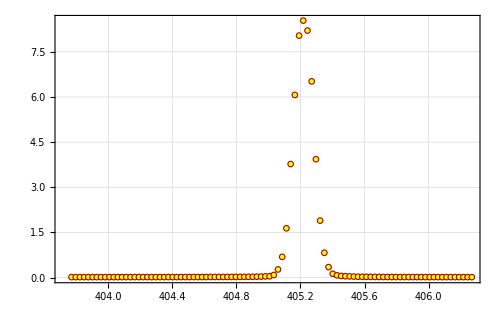

```mathematica
ClearAll["Global`*"];

(*Load CurveFit package*)
curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

(*Hg folder*)
hgDir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files\\real_wavelength_for_curvefit\\Hg_calibration";

files=FileNames["*_REAL_FOR_CURVEFIT.dat",hgDir];

Print["Hg files:"];
Column[FileNameTake/@files]

(*Pick one clean Hg file first,preferably 404.770 or 546.226*)
file=SelectFirst[files,StringContainsQ[#,"404.770"]&];

Print["Using file:"];
Print[file];

data=Import[file,"Table"];
data=Cases[data,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity];

n=Length[data];
xx=data[[All,1]];
yy=data[[All,2]];
sx=ConstantArray[0.,n];
sy=ConstantArray[0.,n];

Print["n = ",n];
Print["x range = ",MinMax[xx]];
Print["y range = ",MinMax[yy]];

LinearDataPlot[]
```

```mathematica
GaussianLFit[]
```

n = 96

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

c= 
0.0178177 | d= 
0.000792837 |  | 
σ_c= 
0.00712897 | σ_d= 
0.0086559 |  | 
y_max= 
8.8619 | μ= 
405.219 | sigma= 
0.0603832 | 
σ_y_max= 
0.0369959 | σ_μ= 
0.000290299 | σ_sigma= 
0.000290438 | Std. deviation= 
0.060868

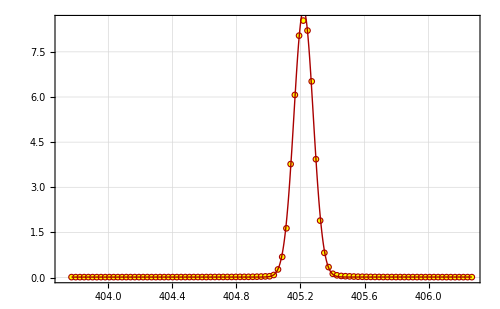
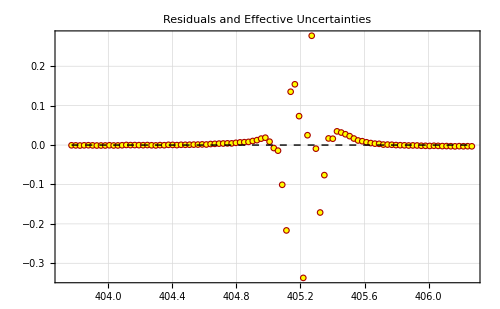
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
0.0178177 | d= 
0.000792837 |  | 
σ_c= 
0.00712897 | σ_d= 
0.0086559 |  | 
y_max= 
8.8619 | μ= 
405.219 | sigma= 
0.0603832 | 
σ_y_max= 
0.0369959 | σ_μ= 
0.000290299 | σ_sigma= 
0.000290438 | Std. deviation= 
0.060868

```mathematica
LinearDifferencePlot[]
```

```mathematica
ClearAll["Global`*"];

(*Load CurveFit package*)
curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

(*Pick one Hg file for test*)
hgDir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files\\real_wavelength_for_curvefit\\Hg_calibration";

file=SelectFirst[FileNames["*_REAL_FOR_CURVEFIT.dat",hgDir],StringContainsQ[#,"404.770"]&];

Print["Using file:"];
Print[file];

(*Import data*)
data=Import[file,"Table"];
data=Cases[data,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity];

(*Set CurveFit global variables*)
n=Length[data];
xx=data[[All,1]];
yy=data[[All,2]];
sx=ConstantArray[0.,n];
sy=ConstantArray[0.,n];

Print["n = ",n];
Print["x range = ",MinMax[xx]];
Print["y range = ",MinMax[yy]];

(*Do Gaussian+linear background fit*)
Quiet[GaussianLFit[],{SetOptions::optnf}];

(*Make full CurveFit fit report:data+fit,residuals,model,parameters*)
fitReport=Quiet[LinearDifferencePlot[],{SetOptions::optnf}];

(*Add clean title*)
titledFitReport=Labeled[fitReport,Style["Hg calibration fit: 404.770 nm line, Gaussian + linear background",14,Black,FontFamily->"Times"],Top];

(*Save PDF*)
outDir=FileNameJoin[{"C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files","Hg_fit_report_TEST"}];

If[!DirectoryQ[outDir],CreateDirectory[outDir]];

outFile=FileNameJoin[{outDir,"TEST_Hg_404p770_GaussianLFit_report.pdf"}];

Export[outFile,titledFitReport,"PDF"];

Print["Saved PDF here:"];
Print[outFile];

SystemOpen[outDir];

(*Also print key fitted numbers for checking*)
Print["Fitted center mean = ",mean];
Print["Center uncertainty sigmean = ",sigmean];
Print["Gaussian sigma = ",sigma];
Print["Sigma uncertainty sigsigma = ",sigsigma];
Print["Residual standard deviation stdv = ",stdv];
```

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Using file:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Hg_calibration\05_Hg_calibration_405.020nm_404.770_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

n = 96

x range = {403.77,406.27}

y range = {0.015274,8.5384}

n = 96

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

c= 
0.0178177 | d= 
0.000792837 |  | 
σ_c= 
0.00712897 | σ_d= 
0.0086559 |  | 
y_max= 
8.8619 | μ= 
405.219 | sigma= 
0.0603832 | 
σ_y_max= 
0.0369959 | σ_μ= 
0.000290299 | σ_sigma= 
0.000290438 | Std. deviation= 
0.060868

Saved PDF here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\Hg_fit_report_TEST\TEST_Hg_404p770_GaussianLFit_report.pdf

Fitted center mean = 405.219

Center uncertainty sigmean = 0.000290299

Gaussian sigma = 0.0603832

Sigma uncertainty sigsigma = 0.000290438

Residual standard deviation stdv = stdv

```mathematica
ClearAll["Global`*"];

(* =======================================================*)
(*PHASE 2:Hg CALIBRATION,FIRST-PASS BASELINE ANALYSIS*)
(* =======================================================*)

(*Load CurveFit package*)
curveFitDir="C:\\Users\\ansht\\Desktop\\package\\CurveFit";
Get[FileNameJoin[{curveFitDir,"CurveFit.m"}]];

(*Input/output folders*)
phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

hgDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hg_calibration"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_firstpass"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];

CreateDirectory[outRoot];

fitReportDir=FileNameJoin[{outRoot,"Hg_GaussianLFit_reports"}];
CreateDirectory[fitReportDir];

calibrationDir=FileNameJoin[{outRoot,"Calibration_outputs"}];
CreateDirectory[calibrationDir];

Print["Hg folder:"];
Print[hgDir];

Print["Output folder:"];
Print[outRoot];


(* =======================================================*)
(*Helper functions*)
(* =======================================================*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[contains_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",hgDir],StringContainsQ[FileNameTake[#],contains]&];
If[Length[matches]==0,Print["NO MATCH FOUND FOR: ",contains];
Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

safeValue[candidates_List]:=Module[{good},good=Select[candidates,Quiet[ValueQ[ToExpression[#]]]&];
If[Length[good]==0,Missing["NotAvailable"],Quiet[ToExpression[First[good]]]]];

getFitParams[]:=<|"c"->safeValue[{"c"}],"sigc"->safeValue[{"sigc","sigC"}],"d"->safeValue[{"d"}],"sigd"->safeValue[{"sigd","sigD"}],"ymax"->safeValue[{"ymax","amp","A"}],"sigymax"->safeValue[{"sigymax","sigamp","sigA"}],"mu"->safeValue[{"mu","mean","μ"}],"sigmu"->safeValue[{"sigmu","sigmean","sigμ"}],"sigma"->safeValue[{"sigma","σ"}],"sigsigma"->safeValue[{"sigsigma","sigσ"}],"stdv"->safeValue[{"stdv","std","standardDeviation"}]|>;

nm[x_]:=ToString[NumberForm[N[x],{Infinity,4},NumberPoint->"."]];

makeCleanTitle[id_,trueWL_,window_]:="Hg calibration fit: "<>id<>", true vacuum wavelength = "<>nm[trueWL]<>" nm"<>", fit window = ["<>nm[window[[1]]]<>", "<>nm[window[[2]]]<>"] nm";

makeOutName[id_]:=StringReplace[id,{"."->"p"," "->"_"}];


(* =======================================================*)
(*Hg fit specifications*)
(* =======================================================*)
(*These windows are first-pass choices.After this runs,inspect the PDFs,especially the 365 nm fits.If a 365 nm fit grabs the wrong nearby Hg peak,we will adjust only that window.*)

hgSpecs={<|"id"->"Hg 365.119","fileKey"->"365.12","trueWL"->365.119,"fitWindow"->{365.45,365.85},"useForCalibration"->True|>,<|"id"->"Hg 365.588","fileKey"->"365.588","trueWL"->365.588,"fitWindow"->{365.70,366.10},"useForCalibration"->True|>,<|"id"->"Hg 404.770","fileKey"->"404.770","trueWL"->404.770,"fitWindow"->{405.00,405.45},"useForCalibration"->True|>,<|"id"->"Hg 546.226","fileKey"->"546.226","trueWL"->546.226,"fitWindow"->{546.25,546.75},"useForCalibration"->True|>};


(* =======================================================*)
(*Fit one Hg line*)
(* =======================================================*)

fitOneHg[spec_]:=Module[{file,dataFull,dataFit,window,trueWL,id,report,titledReport,outFile,params,result},id=spec["id"];
trueWL=spec["trueWL"];
window=spec["fitWindow"];
file=findFile[spec["fileKey"]];
If[MissingQ[file],Return[<|"id"->id,"status"->"file_missing","trueWL_nm"->trueWL,"observed_mu_nm"->Missing["NoFit"],"sigmu_nm"->Missing["NoFit"]|>]];
dataFull=importNumeric[file];
dataFit=cropData[dataFull,window];
If[Length[dataFit]<8,Print["Too few points in fit window for ",id,": ",Length[dataFit]];
Return[<|"id"->id,"status"->"too_few_points","file"->FileNameTake[file],"trueWL_nm"->trueWL,"fitWindow"->ToString[window],"observed_mu_nm"->Missing["NoFit"],"sigmu_nm"->Missing["NoFit"]|>]];
(*CurveFit global variables*)n=Length[dataFit];
xx=dataFit[[All,1]];
yy=dataFit[[All,2]];
sx=ConstantArray[0.,n];
sy=ConstantArray[0.,n];
Print["Fitting ",id," with n = ",n," points."];
Print["File: ",FileNameTake[file]];
Print["Window: ",window];
Quiet[GaussianLFit[],{SetOptions::optnf}];
params=getFitParams[];
report=Quiet[LinearDifferencePlot[],{SetOptions::optnf}];
titledReport=Labeled[report,Style[makeCleanTitle[id,trueWL,window],13,Black,FontFamily->"Times"],Top];
outFile=FileNameJoin[{fitReportDir,makeOutName[id]<>"_GaussianLFit_report.pdf"}];
Export[outFile,titledReport,"PDF"];
result=<|"id"->id,"status"->"fit_complete","file"->FileNameTake[file],"trueWL_nm"->trueWL,"fit_xmin_nm"->window[[1]],"fit_xmax_nm"->window[[2]],"n_fit_points"->n,"observed_mu_nm"->params["mu"],"sigmu_nm"->params["sigmu"],"gaussian_sigma_nm"->params["sigma"],"sigsigma_nm"->params["sigsigma"],"amplitude_ymax"->params["ymax"],"background_c"->params["c"],"background_slope_d"->params["d"],"residual_stdv"->params["stdv"],"useForCalibration"->spec["useForCalibration"],"fit_report_pdf"->outFile|>;
Print["Saved report: ",outFile];
Print["Observed center mu = ",result["observed_mu_nm"]];
Print["sigmu = ",result["sigmu_nm"]];
Print["sigma = ",result["gaussian_sigma_nm"]];
Print["stdv = ",result["residual_stdv"]];
Print["-----------------------------"];
result];


(* =======================================================*)
(*Run Hg fits*)
(* =======================================================*)

hgResults=fitOneHg/@hgSpecs;

hgHeaders=Keys[First[hgResults]];
hgRows=Values/@hgResults;

Export[FileNameJoin[{outRoot,"Hg_peak_fit_results.csv"}],Prepend[hgRows,hgHeaders],"CSV"];

Dataset[hgResults]


(* =======================================================*)
(*Build calibration fit*)
(* =======================================================*)

calRows=Select[hgResults,#["status"]=="fit_complete"&&TrueQ[#["useForCalibration"]]&&NumericQ[#["observed_mu_nm"]]&&NumericQ[#["trueWL_nm"]]&];

calData=({#["observed_mu_nm"],#["trueWL_nm"]}&/@calRows);

Print["Calibration data {observed, true}:"];
Print[calData];

If[Length[calData]<2,Print["Not enough calibration points. Check Hg fits first."],linFit=LinearModelFit[calData,{1,x},x];
linParams=linFit["BestFitParameters"];
aLin=linParams[[1]];
bLin=linParams[[2]];
linResiduals=calData/. {xo_,yt_}:>{xo,yt-linFit[xo]};
linResidualValues=linResiduals[[All,2]];
linRMS=Sqrt[Mean[linResidualValues^2]];
linMaxAbs=Max[Abs[linResidualValues]];
Print["Linear calibration:"];
Print["lambda_true = a + b lambda_obs"];
Print["a = ",aLin];
Print["b = ",bLin];
Print["RMS residual = ",linRMS," nm"];
Print["Max abs residual = ",linMaxAbs," nm"];
quadFit=If[Length[calData]>=3,LinearModelFit[calData,{1,x,x^2},x],Missing["NotEnoughPoints"]];
calibrationSummary={{"model","a","b","c_quadratic","RMS_residual_nm","max_abs_residual_nm"},{"linear",aLin,bLin,"",linRMS,linMaxAbs}};
If[Head[quadFit]=!=Missing,quadParams=quadFit["BestFitParameters"];
quadResiduals=calData/. {xo_,yt_}:>{xo,yt-quadFit[xo]};
quadResidualValues=quadResiduals[[All,2]];
quadRMS=Sqrt[Mean[quadResidualValues^2]];
quadMaxAbs=Max[Abs[quadResidualValues]];
calibrationSummary=Join[calibrationSummary,{{"quadratic",quadParams[[1]],quadParams[[2]],quadParams[[3]],quadRMS,quadMaxAbs}}];];
Export[FileNameJoin[{calibrationDir,"calibration_summary.csv"}],calibrationSummary,"CSV"];
Export[FileNameJoin[{calibrationDir,"calibration_points.csv"}],Prepend[calData,{"observed_mu_nm","true_vacuum_wavelength_nm"}],"CSV"];
calPlot=Show[ListPlot[calData,Frame->True,Axes->False,PlotRange->All,PlotMarkers->Automatic,ImageSize->850,FrameLabel->{"Observed Hg peak center (nm)","True Hg vacuum wavelength (nm)"},PlotLabel->Style["Hg wavelength calibration: true wavelength vs observed peak center",14,Black,FontFamily->"Times"]],Plot[linFit[x],{x,Min[calData[[All,1]]]-0.2,Max[calData[[All,1]]]+0.2}]];
residPlot=ListPlot[linResiduals,Frame->True,Axes->False,PlotRange->All,PlotMarkers->Automatic,ImageSize->850,FrameLabel->{"Observed Hg peak center (nm)","Residual true - linear fit (nm)"},PlotLabel->Style["Hg calibration residuals, linear model",14,Black,FontFamily->"Times"],GridLines->{None,{0}}];
Export[FileNameJoin[{calibrationDir,"Hg_linear_calibration_plot.pdf"}],calPlot,"PDF"];
Export[FileNameJoin[{calibrationDir,"Hg_linear_calibration_residuals.pdf"}],residPlot,"PDF"];
If[Head[quadFit]=!=Missing,quadPlot=Show[ListPlot[calData,Frame->True,Axes->False,PlotRange->All,PlotMarkers->Automatic,ImageSize->850,FrameLabel->{"Observed Hg peak center (nm)","True Hg vacuum wavelength (nm)"},PlotLabel->Style["Hg wavelength calibration: linear vs quadratic check",14,Black,FontFamily->"Times"]],Plot[linFit[x],{x,Min[calData[[All,1]]]-0.2,Max[calData[[All,1]]]+0.2},PlotStyle->Dashed],Plot[quadFit[x],{x,Min[calData[[All,1]]]-0.2,Max[calData[[All,1]]]+0.2}]];
quadResidPlot=Show[ListPlot[linResiduals,Frame->True,Axes->False,PlotMarkers->Automatic,ImageSize->850,FrameLabel->{"Observed Hg peak center (nm)","Residual (nm)"},PlotLabel->Style["Calibration residual comparison: linear residuals",14,Black,FontFamily->"Times"],GridLines->{None,{0}}]];
Export[FileNameJoin[{calibrationDir,"Hg_linear_vs_quadratic_calibration_check.pdf"}],quadPlot,"PDF"];
Export[FileNameJoin[{calibrationDir,"Hg_quadratic_fit_residuals.csv"}],Prepend[quadResiduals,{"observed_mu_nm","true_minus_quadratic_fit_nm"}],"CSV"];];
Print["Calibration outputs saved in:"];
Print[calibrationDir];];

Print["DONE PHASE 2 FIRST PASS."];
Print["Open output folder:"];
Print[outRoot];

SystemOpen[outRoot];
```

SetOptions::optnf: IntervalMarkers is not a known option for ParametricPlot.

Hg folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Hg_calibration

Output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_firstpass

Fitting Hg 365.119 with n = 45 points.

File: 03_Hg_calibration_365.365nm_365.12_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

Window: {365.45,365.85}

n = 45

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

c= 
0.111492 | d= 
2.30243 |  | 
σ_c= 
0.107755 | σ_d= 
0.488035 |  | 
y_max= 
8.07175 | μ= 
365.664 | sigma= 
0.0645556 | 
σ_y_max= 
0.126935 | σ_μ= 
0.00114633 | σ_sigma= 
0.00147053 | Std. deviation= 
0.28718

Saved report: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_firstpass\Hg_GaussianLFit_reports\Hg_365p119_GaussianLFit_report.pdf

Observed center mu = mu

sigmu = sigmu

sigma = 0.0645556

stdv = stdv

-----------------------------

Fitting Hg 365.588 with n = 16 points.

File: 04_Hg_calibration_365.835nm_365.588_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

Window: {365.7,366.1}

n = 16

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

Minimizing Chi^2

FindMinimum::lsbrak: Unable to bracket a minimum along the direction {0,0,0.0052979,0,0} from the point {365.726,6.08158,2.20743,-2.55726,-10.5986}.

General::stop: Further output of FindMinimum::lsbrak will be suppressed during this calculation.

ReplaceAll::reps: {365.703} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {402.273} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 4 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

Part::partw: Part 5 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

Calculating sigy

FindMinimum::srect: Value 1. CurveFit`Private`yymax/.365.703 in search specification {x,ymax,ymax 1.01+1/10.^15} is not a number or array of numbers.

FindMinimum::srect: Value 1. CurveFit`Private`mmean/.CurveFit`Private`mmean in search specification {CurveFit`Private`mmean,mean,mean 1.01+1/10.^15} is not a number or array of numbers.

Calculating sigc

FindMinimum::ioppfa: The value of the option MaxIterations -> 100. should be a positive integer, Infinity or Automatic.

c= 
(1. CurveFit`Private`cc/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,4⟧)+(1. CurveFit`Private`dd/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,5⟧) (-365.703+(1. CurveFit`Private`mmean/.CurveFit`Private`mmean)) | d= 
1. CurveFit`Private`dd/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,5⟧ |  | 
σ_c= 
√(1/4 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.04447 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`cc/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,4⟧])/(CurveFit`Private`e3)]^2+1/4 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.04447 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`mmean/.CurveFit`Private`mmean])/(CurveFit`Private`e3)]^2 (1. CurveFit`Private`dd/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,5⟧)^2+1/4 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.04447 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`dd/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,5⟧])/(CurveFit`Private`e3)]^2 (-365.703+(1. CurveFit`Private`mmean/.CurveFit`Private`mmean))^2) | σ_d= 
1/2 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.04447 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`dd/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,5⟧])/(CurveFit`Private`e3)] |  | 
y_max= 
1. CurveFit`Private`yymax/.365.703 | μ= 
1. CurveFit`Private`mmean/.CurveFit`Private`mmean | sigma= 
1. CurveFit`Private`ssigma/.402.273 | 
σ_y_max= 
1/2 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.04447 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`yymax/.365.703])/(CurveFit`Private`e3)] | σ_μ= 
1/2 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.04447 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`mmean/.CurveFit`Private`mmean])/(CurveFit`Private`e3)] | σ_sigma= 
1/2 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.04447 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`ssigma/.402.273])/(CurveFit`Private`e3)] | Std. deviation= 
0.301511 CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd]

FindMinimum::nrnum: The function value CurveFit`Private`chi[6.91746,0.052979,365.703,0.0504522,-14.0473] is not a real number at {CurveFit`Private`mmean,CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`cc,CurveFit`Private`dd} = {365.703,6.91746,0.052979,0.0504522,-14.0473}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

Set::shape: Lists {Diff,CurveFit`Private`sDiff} and … are not the same shape.

Show::gcomb: Could not combine the graphics objects in Show[«1»,].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Saved report: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_firstpass\Hg_GaussianLFit_reports\Hg_365p588_GaussianLFit_report.pdf

Observed center mu = mu

sigmu = sigmu

sigma = 1. CurveFit`Private`ssigma/.402.273

stdv = stdv

-----------------------------

Fitting Hg 404.770 with n = 17 points.

File: 05_Hg_calibration_405.020nm_404.770_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

Window: {405.,405.45}

n = 17

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

c= 
-0.0201709 | d= 
0.0718476 |  | 
σ_c= 
0.0747198 | σ_d= 
0.348252 |  | 
y_max= 
8.89005 | μ= 
405.219 | sigma= 
0.0607324 | 
σ_y_max= 
0.113009 | σ_μ= 
0.000884177 | σ_sigma= 
0.00104728 | Std. deviation= 
0.164462

Saved report: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_firstpass\Hg_GaussianLFit_reports\Hg_404p770_GaussianLFit_report.pdf

Observed center mu = mu

sigmu = sigmu

sigma = 0.0607324

stdv = stdv

-----------------------------

Fitting Hg 546.226 with n = 20 points.

File: 06_Hg_calibration_546.475nm_546.226_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

Window: {546.25,546.75}

n = 20

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

Part::pkspec1: The expression CurveFit`Private`n1 cannot be used as a part specification.

c= 
(1. CurveFit`Private`cc/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,4⟧)+(1. CurveFit`Private`dd/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,5⟧) (-546.719+(1. CurveFit`Private`mmean/.CurveFit`Private`mmean)) | d= 
1. CurveFit`Private`dd/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,5⟧ |  | 
σ_c= 
√(1/4 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.0328 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`cc/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,4⟧])/(CurveFit`Private`e3)]^2+1/4 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.0328 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`mmean/.CurveFit`Private`mmean])/(CurveFit`Private`e3)]^2 (1. CurveFit`Private`dd/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,5⟧)^2+1/4 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.0328 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`dd/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,5⟧])/(CurveFit`Private`e3)]^2 (-546.719+(1. CurveFit`Private`mmean/.CurveFit`Private`mmean))^2) | σ_d= 
1/2 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.0328 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`dd/.FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,5⟧])/(CurveFit`Private`e3)] |  | 
y_max= 
1. CurveFit`Private`yymax/.546.719 | μ= 
1. CurveFit`Private`mmean/.CurveFit`Private`mmean | sigma= 
1. CurveFit`Private`ssigma/.601.391 | 
σ_y_max= 
1/2 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.0328 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`yymax/.546.719])/(CurveFit`Private`e3)] | σ_μ= 
1/2 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.0328 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`mmean/.CurveFit`Private`mmean])/(CurveFit`Private`e3)] | σ_sigma= 
1/2 Abs[(-CurveFit`Private`e2+√((CurveFit`Private`e2)^2+4 CurveFit`Private`e3 (-CurveFit`Private`e1+1.0328 √((CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd])^2))) Sign[1. CurveFit`Private`ssigma/.601.391])/(CurveFit`Private`e3)] | Std. deviation= 
0.258199 CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd]

Set::shape: Lists {Diff,CurveFit`Private`sDiff} and … are not the same shape.

Saved report: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_firstpass\Hg_GaussianLFit_reports\Hg_546p226_GaussianLFit_report.pdf

Observed center mu = mu

sigmu = sigmu

sigma = 1. CurveFit`Private`ssigma/.601.391

stdv = stdv

-----------------------------

ReplaceAll::reps: {402.273} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {365.703} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

Part::partw: Part 4 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

ReplaceAll::reps: {FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,4⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

Part::partw: Part 5 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

General::stop: Further output of FindMinimum::srect will be suppressed during this calculation.

Part::partw: Part 5 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {402.273} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {365.703} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

Part::partw: Part 4 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

ReplaceAll::reps: {FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,4⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

Part::partw: Part 5 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

General::stop: Further output of FindMinimum::srect will be suppressed during this calculation.

Part::partw: Part 5 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {402.273} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {365.703} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

Part::partw: Part 4 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

ReplaceAll::reps: {FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,4⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

Part::partw: Part 5 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

General::stop: Further output of FindMinimum::srect will be suppressed during this calculation.

Part::partw: Part 5 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {402.273} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {365.703} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

Part::partw: Part 4 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

ReplaceAll::reps: {FindMinimum[CurveFit`Private`chi[CurveFit`Private`yymax,CurveFit`Private`ssigma,CurveFit`Private`mmean,CurveFit`Private`cc,CurveFit`Private`dd],{CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15},{CurveFit`Private`yymax,CurveFit`Private`ymaxinit,CurveFit`Private`ymaxinit 1.1+1/10.^15},{CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15},{CurveFit`Private`cc,CurveFit`Private`cinit,CurveFit`Private`cinit 1.1+1/10.^15},{CurveFit`Private`dd,CurveFit`Private`dinit,CurveFit`Private`dinit 1.1+1/10.^15},MaxIterations→100]⟦2,4⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

Part::partw: Part 5 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

FindMinimum::srect: Value -546.719+{546.257,546.283,546.308,546.334,546.36,546.385,546.411,546.437,546.462,546.488,546.514,546.539,546.565,546.591,546.616,546.642,546.668,546.693,546.719,546.745}⟦CurveFit`Private`n1⟧ in search specification {CurveFit`Private`ssigma,CurveFit`Private`sigmainit,CurveFit`Private`sigmainit 1.1+1/10.^15} is not a number or array of numbers.

General::stop: Further output of FindMinimum::srect will be suppressed during this calculation.

Part::partw: Part 5 of {CurveFit`Private`mmean,CurveFit`Private`meaninit,CurveFit`Private`meaninit 1.1+1/10.^15} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Calibration data {observed, true}:

{}

Not enough calibration points. Check Hg fits first.

DONE PHASE 2 FIRST PASS.

Open output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_firstpass

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Hg_calibration\03_Hg_calibration_365.365nm_365.12_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

Read 284 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> LinearDataPlot, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{365.499,365.893}

n= 45

239 points removed.

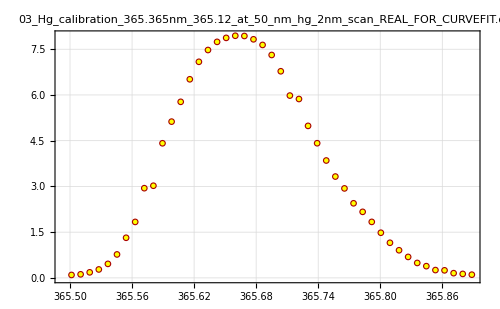

```mathematica
LinearDataPlot[]
```

```mathematica
GaussianLFit[]
```

n = 45

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

c= 
-0.467409 | d= 
3.26663 |  | 
σ_c= 
0.138052 | σ_d= 
0.540603 |  | 
y_max= 
8.54699 | μ= 
365.663 | sigma= 
0.0698867 | 
σ_y_max= 
0.12678 | σ_μ= 
0.0010558 | σ_sigma= 
0.00154909 | Std. deviation= 
0.247532

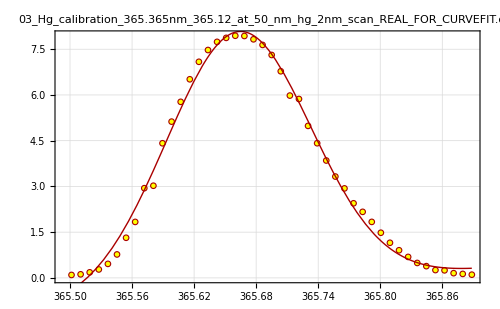
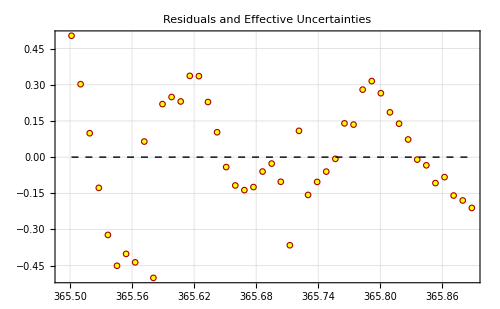
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
-0.467409 | d= 
3.26663 |  | 
σ_c= 
0.138052 | σ_d= 
0.540603 |  | 
y_max= 
8.54699 | μ= 
365.663 | sigma= 
0.0698867 | 
σ_y_max= 
0.12678 | σ_μ= 
0.0010558 | σ_sigma= 
0.00154909 | Std. deviation= 
0.247532

```mathematica
LinearDifferencePlot[]
```

```mathematica
panel=%;

outDir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\CurveFit_appendix\\Hg_calibration_fit_reports";

If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];

outFile=FileNameJoin[{outDir,"CF_Hg_365p119_GaussianLFit_appendix.pdf"}];

Export[outFile,panel,"PDF"];

Print["Saved to:"];
Print[outFile];

SystemOpen[outDir];
```

Saved to:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\CurveFit_appendix\Hg_calibration_fit_reports\CF_Hg_365p119_GaussianLFit_appendix.pdf

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, Nonstandard -> True, DataFunction -> FreqResp]]
]
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Hg_calibration\04_Hg_calibration_365.835nm_365.588_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

Read 95 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> LinearDataPlot, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{365.459,365.924}

n= 18

77 points removed.

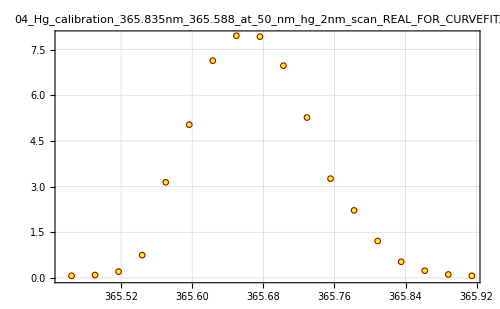

```mathematica
LinearDataPlot[]
```

```mathematica
GaussianLFit[]
```

n = 18

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

c= 
-0.1198 | d= 
1.33087 |  | 
σ_c= 
0.155108 | σ_d= 
0.622861 |  | 
y_max= 
8.3495 | μ= 
365.664 | sigma= 
0.0680803 | 
σ_y_max= 
0.203435 | σ_μ= 
0.00187304 | σ_sigma= 
0.00238003 | Std. deviation= 
0.299905

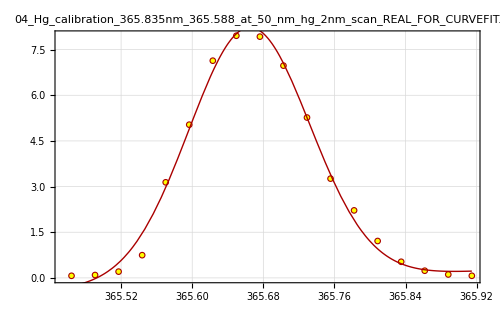
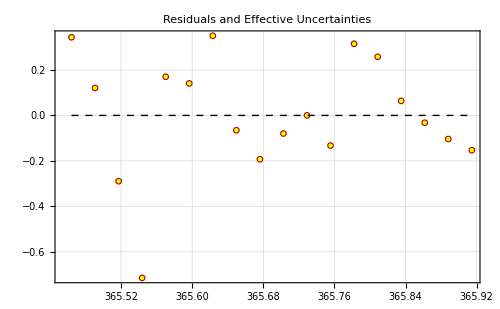
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
-0.1198 | d= 
1.33087 |  | 
σ_c= 
0.155108 | σ_d= 
0.622861 |  | 
y_max= 
8.3495 | μ= 
365.664 | sigma= 
0.0680803 | 
σ_y_max= 
0.203435 | σ_μ= 
0.00187304 | σ_sigma= 
0.00238003 | Std. deviation= 
0.299905

```mathematica
LinearDifferencePlot[]
```

```mathematica
panel=%;

outDir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\CurveFit_appendix\\Hg_calibration_fit_reports";

If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];

outFile=FileNameJoin[{outDir,"CF_Hg_365p588_GaussianLFit_appendix.pdf"}];

Export[outFile,panel,"PDF"];

Print["Saved to:"];
Print[outFile];

SystemOpen[outDir];
```

Saved to:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\CurveFit_appendix\Hg_calibration_fit_reports\CF_Hg_365p588_GaussianLFit_appendix.pdf

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name, Nonstandard -> True, DataFunction -> FreqResp]]
]
```

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Hg_calibration\05_Hg_calibration_405.020nm_404.770_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

Read 96 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> LinearDataPlot, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{405.007,405.45}

n= 16

80 points removed.

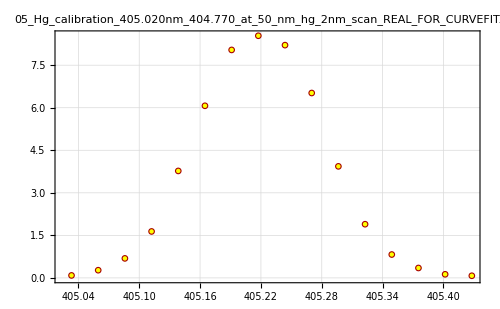

```mathematica
LinearDataPlot[]
```

```mathematica
GaussianLFit[]
```

n = 16

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

c= 
-0.0387075 | d= 
0.161479 |  | 
σ_c= 
0.0884528 | σ_d= 
0.413177 |  | 
y_max= 
8.90415 | μ= 
405.219 | sigma= 
0.0608969 | 
σ_y_max= 
0.120943 | σ_μ= 
0.000943893 | σ_sigma= 
0.00115406 | Std. deviation= 
0.170225

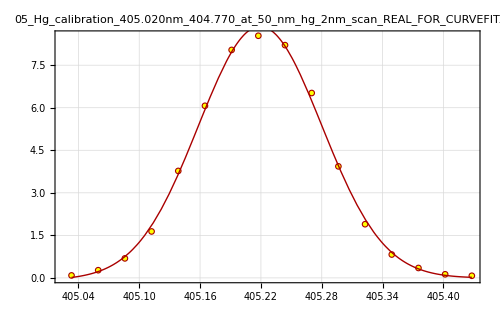
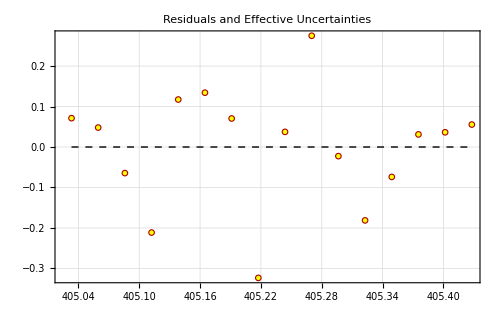
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
-0.0387075 | d= 
0.161479 |  | 
σ_c= 
0.0884528 | σ_d= 
0.413177 |  | 
y_max= 
8.90415 | μ= 
405.219 | sigma= 
0.0608969 | 
σ_y_max= 
0.120943 | σ_μ= 
0.000943893 | σ_sigma= 
0.00115406 | Std. deviation= 
0.170225

```mathematica
LinearDifferencePlot[]
```

```mathematica
panel = %;

outDir = "C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\CurveFit_appendix\\Hg_calibration_fit_reports";

If[! DirectoryQ[outDir], 
  CreateDirectory[outDir, CreateIntermediateDirectories -> True]
];

outFile = FileNameJoin[{outDir, "CF_Hg_404p770_GaussianLFit_appendix.pdf"}];

Export[outFile, panel, "PDF"];

Print["Saved to:"];
Print[outFile];

SystemOpen[outDir];
```

Saved to:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\CurveFit_appendix\Hg_calibration_fit_reports\CF_Hg_404p770_GaussianLFit_appendix.pdf

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Hg_calibration\06_Hg_calibration_546.475nm_546.226_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

Read 98 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> LinearDataPlot, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

$Canceled

XRangeKeep[$Canceled]

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Hg_calibration\06_Hg_calibration_546.475nm_546.226_at_50_nm_hg_2nm_scan_REAL_FOR_CURVEFIT.dat

Read 98 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> LinearDataPlot, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{546.487,546.948}

n= 18

80 points removed.

```mathematica
GaussianLFit[]
```

n = 18

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

c= 
-0.0281032 | d= 
0.0575953 |  | 
σ_c= 
0.0169269 | σ_d= 
0.0695301 |  | 
y_max= 
2.40869 | μ= 
546.708 | sigma= 
0.0691664 | 
σ_y_max= 
0.022317 | σ_μ= 
0.000729859 | σ_sigma= 
0.000905784 | Std. deviation= 
0.0333459

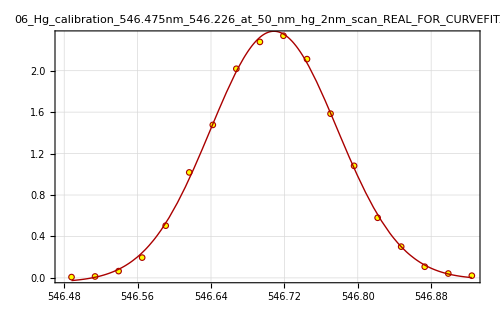
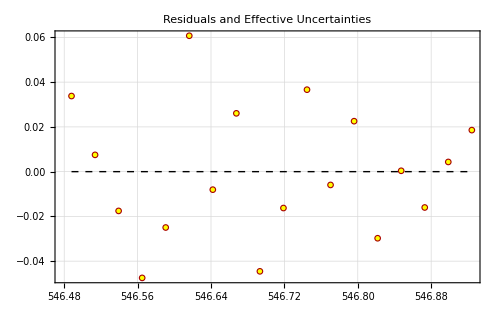
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
-0.0281032 | d= 
0.0575953 |  | 
σ_c= 
0.0169269 | σ_d= 
0.0695301 |  | 
y_max= 
2.40869 | μ= 
546.708 | sigma= 
0.0691664 | 
σ_y_max= 
0.022317 | σ_μ= 
0.000729859 | σ_sigma= 
0.000905784 | Std. deviation= 
0.0333459

```mathematica
LinearDifferencePlot[]
```

```mathematica
panel=%;

outDir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\CurveFit_appendix\\Hg_calibration_fit_reports";

If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];

outFile=FileNameJoin[{outDir,"CF_Hg_546p226_GaussianLFit_appendix.pdf"}];

Export[outFile,panel,"PDF"];

Print["Saved to:"];
Print[outFile];

SystemOpen[outDir];
```

Saved to:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\CurveFit_appendix\Hg_calibration_fit_reports\CF_Hg_546p226_GaussianLFit_appendix.pdf

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Hg_calibration\07_Hg_calibration_546.250nm_562hg_2nm_scan_REAL_FOR_CURVEFIT.dat

Read 293 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> LinearDataPlot, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{546.519,546.91}

n= 46

247 points removed.

```mathematica
GaussianLFit[]
```

n = 46

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

c= 
-0.128294 | d= 
0.499986 |  | 
σ_c= 
0.0283794 | σ_d= 
0.108283 |  | 
y_max= 
2.81276 | μ= 
546.696 | sigma= 
0.0723973 | 
σ_y_max= 
0.0272381 | σ_μ= 
0.000724073 | σ_sigma= 
0.000990265 | Std. deviation= 
0.0543793

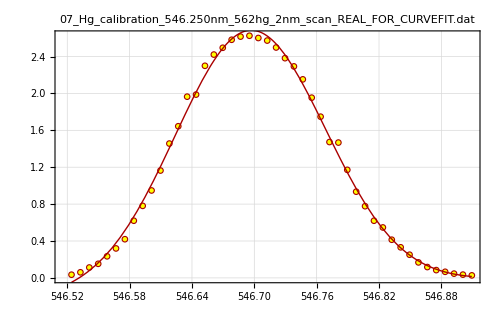
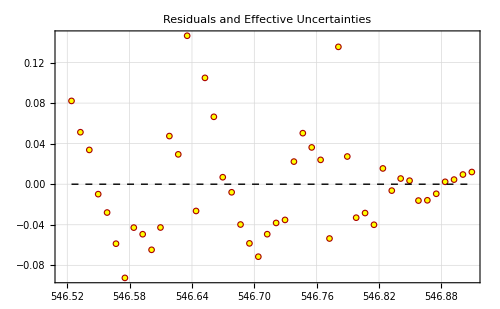
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
-0.128294 | d= 
0.499986 |  | 
σ_c= 
0.0283794 | σ_d= 
0.108283 |  | 
y_max= 
2.81276 | μ= 
546.696 | sigma= 
0.0723973 | 
σ_y_max= 
0.0272381 | σ_μ= 
0.000724073 | σ_sigma= 
0.000990265 | Std. deviation= 
0.0543793

```mathematica
LinearDifferencePlot[]
```

```mathematica
panel = %;

outDir = "C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\CurveFit_appendix\\Hg_calibration_fit_reports";

If[! DirectoryQ[outDir], 
  CreateDirectory[outDir, CreateIntermediateDirectories -> True]
];

outFile = FileNameJoin[{outDir, "CF_Hg_546_repeat_wide_scan_appendix.pdf"}];

Export[outFile, panel, "PDF"];

Print["Saved to:"];
Print[outFile];

SystemOpen[outDir];
```

Saved to:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\CurveFit_appendix\Hg_calibration_fit_reports\CF_Hg_546_repeat_wide_scan_appendix.pdf

```mathematica
With[  {name = SystemDialogInput["FileOpen",{DataFileName,{"data files"->{"*.dat", "*.mca"},"all files"->{"*"}}}]},
  If[ name =!= $Canceled, 
    LoadFile[name]]
]
```

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Hg_calibration\15_Hg_calibration_546.250nm_same_data_as_562hg_2nm_scan_but_slit_width_is_20_nm_REAL_FOR_CURVEFIT.dat

Read 293 data points.

Change the plot from LinearDataPlot[ ] to something else like LogDataPlot[ ] if you wish. If the plot has a log X-axis (like LogLogDataPlot[ ]), then the Log option to SetXRange[ ] must be changed to Log → True

```mathematica
With[{x = SetXRange[ LinearDataPlot[], Log -> LinearDataPlot, Label -> "Set the X values for the range you wish to keep." ]}, 
  Print[x]; 

  XRangeKeep[Sequence@@x] 
]
```

{546.542,546.902}

n= 42

251 points removed.

```mathematica
GaussianLFit[]
```

n = 42

y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)

Fit of (x,y) (unweighted):

c= 
-0.385949 | d= 
1.94741 |  | 
σ_c= 
0.0857698 | σ_d= 
0.332092 |  | 
y_max= 
2.47556 | μ= 
546.683 | sigma= 
0.0745503 | 
σ_y_max= 
0.08174 | σ_μ= 
0.00163242 | σ_sigma= 
0.0026288 | Std. deviation= 
0.0759889

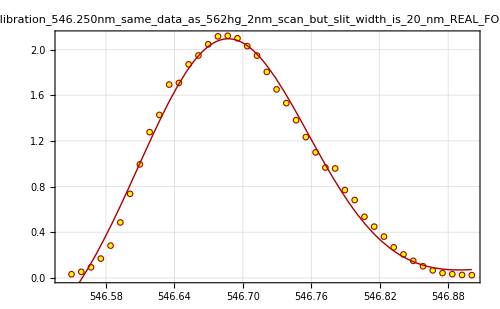
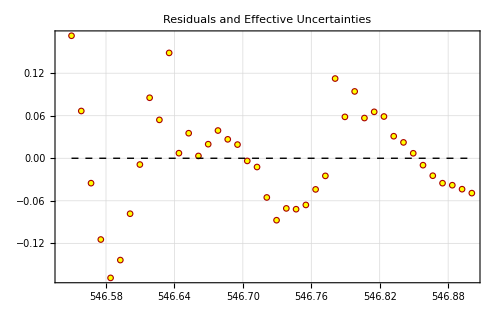
-Graphics-
-Graphics-
y(x) =
y_max exp (-(x - μ)^2/2 sigma^2)  +
c + d (x - μ)
c= 
-0.385949 | d= 
1.94741 |  | 
σ_c= 
0.0857698 | σ_d= 
0.332092 |  | 
y_max= 
2.47556 | μ= 
546.683 | sigma= 
0.0745503 | 
σ_y_max= 
0.08174 | σ_μ= 
0.00163242 | σ_sigma= 
0.0026288 | Std. deviation= 
0.0759889

```mathematica
LinearDifferencePlot[]
```

```mathematica
panel=%;

outDir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\CurveFit_appendix\\Hg_calibration_fit_reports";

If[!DirectoryQ[outDir],CreateDirectory[outDir,CreateIntermediateDirectories->True]];

outFile=FileNameJoin[{outDir,"CF_Hg_546_repeat_20um_slit_appendix.pdf"}];

Export[outFile,panel,"PDF"];

Print["Saved to:"];
Print[outFile];

SystemOpen[outDir];
```

Saved to:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\CurveFit_appendix\Hg_calibration_fit_reports\CF_Hg_546_repeat_20um_slit_appendix.pdf

```mathematica
ClearAll["Global`*"];

(* =========================================*)
(*PHASE 2:NATIVE MATHEMATICA Hg CALIBRATION*)
(*Main-report numerical analysis*)
(* =========================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

hgDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hg_calibration"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

fitDir=FileNameJoin[{outRoot,"Hg_native_fit_reports"}];
calDir=FileNameJoin[{outRoot,"Calibration_outputs"}];

CreateDirectory[fitDir];
CreateDirectory[calDir];

Print["Output folder: ",outRoot];


(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",hgDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

fmt[x_]:=ToString[NumberForm[N[x],{Infinity,6},NumberPoint->"."]];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];


(*----------Hg specs----------*)
(*Use 365.588,404.770,546.226 as main calibration points.The 365.119 scan is saved as diagnostic only because it appears crowded/ambiguous.The repeated 546 scans are repeatability checks,not independent calibration lines.*)

hgSpecs={<|"id"->"Hg 365.119 diagnostic","fileKey"->"365.12","trueWL"->365.119,"window"->{365.50,365.85},"useForCalibration"->False|>,<|"id"->"Hg 365.588","fileKey"->"365.588","trueWL"->365.588,"window"->{365.50,365.90},"useForCalibration"->True|>,<|"id"->"Hg 404.770","fileKey"->"404.770","trueWL"->404.770,"window"->{405.05,405.42},"useForCalibration"->True|>,<|"id"->"Hg 546.226","fileKey"->"546.226","trueWL"->546.226,"window"->{546.50,546.92},"useForCalibration"->True|>,<|"id"->"Hg 546 repeat wide","fileKey"->"562hg_2nm_scan","trueWL"->546.226,"window"->{546.55,546.90},"useForCalibration"->False|>,<|"id"->"Hg 546 repeat 20um","fileKey"->"same_data","trueWL"->546.226,"window"->{546.55,546.90},"useForCalibration"->False|>};


(*----------fit one peak----------*)

fitOneHg[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,c0,d0,amp0,mu0,sig0,x0,fit,params,errs,resid,rms,maxresid,fitPlot,residPlot,table,report,outFile,c,d,amp,mu,sig,x},file=findFile[spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["id"]];
Return[<|"id"->spec["id"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<8,Print["Too few points for ",spec["id"]];
Return[<|"id"->spec["id"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
x0=Mean[{xmin,xmax}];
c0=Median[Join[Take[yvals,UpTo[5]],Take[yvals,-UpTo[5]]]];
d0=0;
amp0=Max[yvals]-c0;
mu0=xvals[[First@Ordering[yvals,-1]]];
sig0=(xmax-xmin)/6;
fit=Quiet@NonlinearModelFit[data,c+d (x-x0)+amp Exp[-(x-mu)^2/(2 sig^2)],{{c,c0},{d,d0},{amp,amp0},{mu,mu0},{sig,sig0}},x,MaxIterations->10000];
params=fit["BestFitParameters"];
errs=fit["ParameterErrors"];
resid=data/. {xx_,yy_}:>{xx,yy-fit[xx]};
rms=Sqrt[Mean[resid[[All,2]]^2]];
maxresid=Max[Abs[resid[[All,2]]]];
fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,8},PlotRange->All,ImageSize->750,FrameLabel->{"Wavelength (nm)","Signal (V)"},PlotLabel->Style[spec["id"]<>": Gaussian + linear background",14,Black]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}]];
residPlot=ListPlot[resid,Frame->True,Axes->False,PlotMarkers->{Automatic,8},PlotRange->All,ImageSize->750,FrameLabel->{"Wavelength (nm)","Residual (V)"},PlotLabel->Style["Residuals",13,Black],GridLines->{None,{0}}];
table=Grid[{{"parameter","estimate","standard error"},{"c",c/. params,errs[[1]]},{"d",d/. params,errs[[2]]},{"amp",amp/. params,errs[[3]]},{"mu",mu/. params,errs[[4]]},{"sigma",sig/. params,errs[[5]]},{"RMS residual",rms,""},{"max |residual|",maxresid,""},{"true Hg wavelength",spec["trueWL"],""},{"used for calibration?",spec["useForCalibration"],""}},Frame->All,Alignment->Left];
report=Column[{Style["Native Mathematica fit report: "<>spec["id"],16,Bold],Style["File: "<>FileNameTake[file],10],Style["Fit window: "<>ToString[spec["window"]]<>" nm",10],fitPlot,residPlot,table},Spacings->1];
outFile=FileNameJoin[{fitDir,makeName[spec["id"]]<>"_native_fit_report.pdf"}];
Export[outFile,report,"PDF"];
<|"id"->spec["id"],"status"->"fit_complete","file"->FileNameTake[file],"trueWL_nm"->spec["trueWL"],"fit_xmin_nm"->xmin,"fit_xmax_nm"->xmax,"n_points"->Length[data],"mu_obs_nm"->(mu/. params),"mu_SE_nm"->errs[[4]],"sigma_nm"->(sig/. params),"sigma_SE_nm"->errs[[5]],"amp"->(amp/. params),"amp_SE"->errs[[3]],"background_c"->(c/. params),"background_d"->(d/. params),"rms_residual"->rms,"max_abs_residual"->maxresid,"useForCalibration"->spec["useForCalibration"],"report_pdf"->outFile|>];


(*----------run fits----------*)

results=fitOneHg/@hgSpecs;

Export[FileNameJoin[{outRoot,"Hg_native_peak_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

Dataset[results]


(*----------calibration fit----------*)

calRows=Select[results,#["status"]=="fit_complete"&&TrueQ[#["useForCalibration"]]&];

calData=({#["mu_obs_nm"],#["trueWL_nm"]}&/@calRows);

linCal=LinearModelFit[calData,{1,x},x];

calParams=linCal["BestFitParameters"];
calErrors=linCal["ParameterErrors"];

a=calParams[[1]];
b=calParams[[2]];

sigmaA=calErrors[[1]];
sigmaB=calErrors[[2]];

calResiduals=calData/. {xo_,yt_}:>{xo,yt-linCal[xo]};
resVals=calResiduals[[All,2]];

rmsCal=Sqrt[Mean[resVals^2]];
maxCal=Max[Abs[resVals]];

calSummary={{"quantity","value"},{"a_intercept_nm",a},{"sigma_a_nm",sigmaA},{"b_slope",b},{"sigma_b",sigmaB},{"RMS_residual_nm",rmsCal},{"max_abs_residual_nm",maxCal}};

Export[FileNameJoin[{calDir,"Hg_linear_calibration_summary.csv"}],calSummary,"CSV"];

Export[FileNameJoin[{calDir,"Hg_calibration_points.csv"}],Prepend[calData,{"observed_mu_nm","true_vacuum_wavelength_nm"}],"CSV"];

Export[FileNameJoin[{calDir,"Hg_linear_calibration_residuals.csv"}],Prepend[calResiduals,{"observed_mu_nm","true_minus_fit_nm"}],"CSV"];

calPlot=Show[ListPlot[calData,Frame->True,Axes->False,PlotMarkers->{Automatic,10},ImageSize->800,FrameLabel->{"Observed Hg center (nm)","True Hg vacuum wavelength (nm)"},PlotLabel->Style["Hg calibration: true wavelength vs observed center",14,Black]],Plot[linCal[x],{x,Min[calData[[All,1]]]-0.5,Max[calData[[All,1]]]+0.5},PlotStyle->{Red,Thick}]];

residPlot=ListPlot[calResiduals,Frame->True,Axes->False,PlotMarkers->{Automatic,10},ImageSize->800,FrameLabel->{"Observed Hg center (nm)","Residual true - fit (nm)"},PlotLabel->Style["Hg calibration residuals",14,Black],GridLines->{None,{0}}];

Export[FileNameJoin[{calDir,"Hg_linear_calibration_plot.pdf"}],calPlot,"PDF"];
Export[FileNameJoin[{calDir,"Hg_linear_calibration_residuals.pdf"}],residPlot,"PDF"];

Print["Linear calibration:"];
Print["lambda_true = a + b lambda_obs"];
Print["a = ",a," ± ",sigmaA];
Print["b = ",b," ± ",sigmaB];
Print["RMS residual = ",rmsCal," nm"];
Print["Max abs residual = ",maxCal," nm"];

Print["DONE. Open output folder:"];
Print[outRoot];

SystemOpen[outRoot];
```

Output folder: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_native

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]].

Join::heads: Heads List and Take at positions 1 and 2 are expected to be the same.

NonlinearModelFit::srect: Value Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]] in search specification {c$193557,Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

Part::partw: Part 4 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]].

Join::heads: Heads List and Take at positions 1 and 2 are expected to be the same.

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n} or {m, n, s}) expected at position 2 in Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]].

General::stop: Further output of Take::seqs will be suppressed during this calculation.

Join::heads: Heads List and Take at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

NonlinearModelFit::srect: Value Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]] in search specification {c$193557,Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]] in search specification {c$193557,Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]]} is not a number or array of numbers.

Part::partw: Part 4 of … does not exist.

NonlinearModelFit::srect: Value Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]] in search specification {c$193557,Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 5 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::srect: Value Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]] in search specification {c$193557,Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]] in search specification {c$193557,Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]]} is not a number or array of numbers.

Part::partw: Part 4 of … does not exist.

NonlinearModelFit::srect: Value Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]] in search specification {c$193557,Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 5 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::srect: Value Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]] in search specification {c$193557,Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]] in search specification {c$193557,Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]]} is not a number or array of numbers.

Part::partw: Part 4 of … does not exist.

NonlinearModelFit::srect: Value Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]] in search specification {c$193557,Median[Join[{0.096539,0.117218,0.182402,0.276753,0.459633},Take[{0.096539,0.117218,0.182402,0.276753,0.459633,0.769348,1.31619,1.83588,2.94213,3.02272,4.41529,5.12514,5.77473,6.51402,7.0875,7.47395,7.7414,7.87209,7.94198,7.9343,7.825,7.64058,7.31113,6.77698,5.97963,5.86716,4.98567,4.41683,3.85011,3.32373,2.93484,2.44658,2.16634,1.83687,1.48104,1.15199,0.906565,0.687811,0.490192,0.385027},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 5 of … does not exist.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partw: Part 3 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dataset[<>]

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of … does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of … does not exist.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of … does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of … does not exist.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of … does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of … does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

Part::partw: Part 2 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::srect: Value Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]] in search specification {c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{0.20578,0.746534,3.14052,5.03368,7.13623,7.95573,7.92609,6.97351,5.26851,3.26132,2.21785,1.21204,0.529846,0.235804,0.111867},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{365.517,0.20578},{365.544,0.746534},{365.57,3.14052},{365.597,5.03368},{365.623,7.13623},{365.65,7.95573},{365.676,7.92609},{365.703,6.97351},{365.729,5.26851},{365.756,3.26132},{365.782,2.21785},{365.809,1.21204},{365.835,0.529846},{365.862,0.235804},{365.888,0.111867}},c$496169+amp$496169 ⅇ^(-Plus[«2»]^2/(2 sig$496169^2))+d$496169 (-365.703+x$496169),{{c$496169,Median[Join[{0.20578,0.746534,3.14052,5.03368,7.13623},Take[{«15»},Times[«2»]]]]},{d$496169,0},{amp$496169,7.95573-Median[Join[«2»]]},{mu$496169,365.65},{sig$496169,0.0618093}},x$496169,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]] in search specification {c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{0.271003,0.68772,1.63761,3.77175,6.06884,8.03831,8.5384,8.2075,6.5194,3.93281,1.8928,0.823905,0.349406,0.126887},-UpTo[5]]]]} is not a number or array of numbers.

ReplaceAll::reps: {NonlinearModelFit[{{405.06,0.271003},{405.086,0.68772},{405.112,1.63761},{405.138,3.77175},{405.165,6.06884},{405.191,8.03831},{405.217,8.5384},{405.244,8.2075},{405.27,6.5194},{405.296,3.93281},{405.323,1.8928},{405.349,0.823905},{405.375,0.349406},{405.402,0.126887}},c$598576+amp$598576 ⅇ^(-Plus[«2»]^2/(2 sig$598576^2))+d$598576 (-405.231+x$598576),{{c$598576,Median[Join[{0.271003,0.68772,1.63761,3.77175,6.06884},Take[{«14»},Times[«2»]]]]},{d$598576,0},{amp$598576,8.5384-Median[Join[«2»]]},{mu$598576,405.217},{sig$598576,0.0570163}},x$598576,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::srect: Value Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]] in search specification {c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{0.013681,0.065464,0.195825,0.504077,1.01808,1.47673,2.0187,2.27781,2.33742,2.11175,1.58501,1.08176,0.580413,0.301614,0.107766,0.04218},-UpTo[5]]]]} is not a number or array of numbers.

General::stop: Further output of NonlinearModelFit::srect will be suppressed during this calculation.

ReplaceAll::reps: {NonlinearModelFit[{{546.514,0.013681},{546.539,0.065464},{546.565,0.195825},{546.591,0.504077},{546.616,1.01808},{546.642,1.47673},{546.668,2.0187},{546.693,2.27781},{546.719,2.33742},{546.745,2.11175},{546.77,1.58501},{546.796,1.08176},{546.822,0.580413},{546.847,0.301614},{546.873,0.107766},{546.899,0.04218}},c$694932+amp$694932 ⅇ^(-Plus[«2»]^2/(2 sig$694932^2))+d$694932 (-546.706+x$694932),{{c$694932,Median[Join[{0.013681,0.065464,0.195825,0.504077,1.01808},Take[{«16»},Times[«2»]]]]},{d$694932,0},{amp$694932,2.33742-Median[Join[«2»]]},{mu$694932,546.719},{sig$694932,0.0641732}},x$694932,MaxIterations→10000][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of … does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

Part::partw: Part 2 of … does not exist.

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

General::stop: Further output of LinearModelFit::desmat will be suppressed during this calculation.

Part::partw: Part 2 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.